# QNM Amplitude: Time and Frequency domain analysis

```mathematica
Quit[]
```

```mathematica
Clear["Global`*"]
<<MaTeX`
SetDirectory[NotebookDirectory[]];
$Assumptions={M>0}
DirName=NotebookDirectory[];
```

{M>0}

## Parameters

## Physical Parameters

### Wave equation Parameters

```mathematica
Mbh=rh/2;
λ=rh;
spin=2;
l=2;
```

### Bump Parameters

```mathematica
ModelName="BumpPT";
 ao= 115722/10000; (*120000/10000;*)
 ϵ=204/100000;
```

### Gauss ID Paramers

```mathematica
λg=1 * Mbh;
rg=100 * Mbh;
```

## Numerical Parameters

```mathematica
Prec=10*MachinePrecision;

Nz$Gauss=150;
Nz$Bumb=150;


Nz$QNMload$dom0=75;
Nz$QNMload$dom1=75;
```

### QNM Selection

```mathematica
N$QNM$max=8;
```

## Schwarzschild Spacetime

## Metric Function

```mathematica
a=1-rh/r;
b=a;
f=FullSimplify[Sqrt[a*b], Assumptions->{rh>0, r>rh}];
ζ$of$r=FullSimplify[Sqrt[a/b], Assumptions->{rh>0, r>rh}];
```

```mathematica
m=r/2*(1-b);

fAsymp=Normal@Series[f,{r,Infinity,1}]//Expand;
M$ADM=-Coefficient[fAsymp,r,-1]/2//FullSimplify;
SubsM={M->M$ADM}
```

{M→rh/2}

## Hyperboloidal Formulation

## Radial Compactfication

### Areal Radius

```mathematica
ρ1=0;(*rh/λ 1/(1-σ0)*)
ρ0=rh/λ-ρ1;

ρ[σ_]:=ρ0+ρ1*σ
β=ρ[σ]-σ*D[ρ[σ],σ]//FullSimplify;
```

### Radial Mapping

```mathematica
r$of$σ[σ_]:=λ ρ[σ]/σ;
dr$dσ=D[r$of$σ[σ],σ];

σ$of$r=σ/.Solve[r$of$σ[σ]==r,σ][[1]];
```

```mathematica
σh=σhrz/.Solve[r$of$σ[σhrz]==rh,σhrz][[1]];
```

### Metric function and deviation function in compact coordinate

```mathematica
F=Simplify[f/.r->r$of$σ[σ]];
ζ=Simplify[ζ$of$r/.r->r$of$σ[σ]];
```

#### Find Horizons

```mathematica
SubsσHrz=Solve[{F==0, σ>0},σ,Reals];
σHrz=σ/.SubsσHrz;
nHrz=Length@σHrz;
rHrz=r$of$σ[σHrz];
```

#### Representation as in eq. 2.13 - Event Horizon

```mathematica
root$rh=(1-rHrz/r)/.r->r$of$σ[σ]//FullSimplify;
Kh=Expand[F/root$rh]//FullSimplify;
```

## Dimensionless Tortoise Coordinate

### Differential Equation (eq. 2.11)

```mathematica
dx$dσ=FullSimplify[-β/(σ^2F)];
```

### Contribution from Infinity (eq. 4.7)

```mathematica
x$0=ρ0/σ-2M/λ Log[σ];
dx0$dσ=FullSimplify[D[x$0,σ]];
```

### Contribution from Event Horizon (eq. 4.5)

```mathematica
KBHHrz=Table[Limit[Kh[[i]],SubsσHrz[[i]]],{i,1,nHrz}];
x$BHHrz=Table[rHrz[[i]]/(λ*KBHHrz[[i]])*Log[σHrz[[i]]-σ],{i,1,nHrz}];

dx$BHHrz$dσ=Table[D[x$BHHrz[[i]],σ],{i,1,nHrz}];
```

### Regular Contribution

```mathematica
dx$dσ$Reg=dx$dσ-dx0$dσ - Sum[dx$BHHrz$dσ[[i]],{i,1,nHrz}]/.SubsM;
Subs$dxdσ$Reg=x$Reg'[σ]->dx$dσ$Reg;
```

#### Check Tortoise

```mathematica
x$Reg[σ_]:=0;
x=x$0+ Sum[x$BHHrz[[i]],{i,1,nHrz}]+x$Reg[σ]/.SubsM//Simplify;

rStar=λ*x;

dx$dσ$Paper=D[x,σ]/.Subs$dxdσ$Reg;
FullSimplify[dx$dσ$Paper==dx$dσ]
```

True

## Height Function

### Out-In Strategy

```mathematica
H=-x$0 +Sum[x$BHHrz[[i]],{i,1,nHrz}]-x$Reg[σ]/.SubsM//Simplify;
dH$dσ=D[H,σ]/.Subs$dxdσ$Reg;
```

### Metric Functions

```mathematica
p=FullSimplify[-1/dx$dσ]
(*Plot[p/.λ->rh//Simplify,{σ,0,σHrz[[1]]}, WorkingPrecision->100, PlotRange->All]*)
```

-((-1+σ) σ^2)

```mathematica
γ=dH$dσ*p//FullSimplify
(*Plot[γ/.λ->rh//Simplify,{σ,0,σHrz[[1]]}, WorkingPrecision->100, PlotRange->All]*)
```

1-2 σ^2

```mathematica
(*Series[γ,{σ,σHrz[[1]],0}]*)
w=(1-γ^2)/p//FullSimplify
(*Plot[w/.λ->rh//Simplify,{σ,0,σHrz[[1]]}, WorkingPrecision->100, PlotRange->{0,All}]*)
```

4 (1+σ)

## Wave Equation

## Regge Wheeler Potential

```mathematica
If[spin==0,VRW=a/r^2*(l*(l+1) + r*D[a*b,r]/(2*a))];
If[Abs@spin==2, VRW=a/r^2* ( l*(l+1) - 6m/r + D[m,r])];

qRW=λ^2/p * VRW/.r->r$of$σ[σ]//FullSimplify
```

6-3 σ

### Bump

```mathematica
Vbump =  λ^(-2) Sech[x-ao]^2/.r->r$of$σ[σ]//FullSimplify;
(* λ^(-2) Exp[ -(x-ao)^2/(2 δ)  ]*)

qBump=λ^2/p * Vbump;
```

```mathematica
If[ϵ==0,
σBump=1/2,
σBump=σ/.N[Solve[x-ao==0,σ],50*MachinePrecision][[1]]
];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

### Gauss ID

```mathematica
σGaussID=σ$of$r/.r->rg;
rrg=rStar/.σ->σGaussID;
```

### Final Potential

```mathematica
V = VRW + ϵ Vbump/.r->r$of$σ[σ];
q = λ^2/p * V//FullSimplify;
```

## Functions in Wave Equation

```mathematica
W=w;

α2=p;
α1=D[p,σ];
α0=-q;

β1=2 γ;
β0=D[γ,σ];
```

## QNM Eigenfunctions

## Discrete Functions and Matrices

### AnMR

```mathematica
x$of$χ[χ_,κ_,xb_]:= xb(1- 2 Sinh[ κ (1-xb χ)]/Sinh[2κ]    );
χ$of$x[X_,κ_,xb_]:=xb*(1-ArcSinh[(1 - X*xb)*Sinh[2κ]/2]/κ);
```

### Spectral Routines

#### Chebyshev Coefficients

```mathematica
ChebGaussCoefficients[f_, Prec_]:=Module[
{nf, Nf,c,x},
nf=Length@f;
Nf=nf-1;

x[j_]:=N[ Cos[Pi*(j+1/2)/(Nf+1)] ,Prec];

c=Table[  2 Sum[f[[j+1]]*ChebyshevT[m,x[j]],{j,0,Nf}]  /nf        ,{m,0,Nf}]
];

ChebLobattoCoefficients[f_, Prec_]:=Module[
{nf, Nf,c,x},
nf=Length@f;
Nf=nf-1;

x[j_]:=N[Cos[j π/Nf],Prec];

c=Table[  ( 2-KroneckerDelta[m,Nf]) /(2Nf) (  f[[1]]+(-1)^m f[[nf]] + 2 Sum[f[[j+1]]*ChebyshevT[m,x[j]],{j,1,Nf-1}]  )        ,{m,0,Nf}]
];
```

#### Spectral Differentiation matrices

```mathematica
DiffMatrix[a_,b_,Nz_,Prec_]:=Module[
{k,i,j,dx, Δ,Dy},

k[i_]:=If[i*(i-Nz)==0, 2,1];
dx[i_,j_]:=If[i!=j,
k[i]*(-1)^(i-j)/(k[j]*(x[i,Nz]-x[j,Nz])),
0
];
Δ=b-a;
Dy=N[2/Δ * Table[dx[i,j], {i,0,Nz}, {j,0,Nz}],Prec ];

For[i=0, i<=Nz, i++,
Dy[[i+1,i+1]]= -Sum[ Dy[[i+1,j+1]], {j,0,Nz} ];
];
Dy
]
```

#### Chebyshev Interpolation

```mathematica
ChebInterpolation[c_,a_,b_,x_, κ_, xb_, Prec_]:=Module[
{nc, Nc, χ, y},
nc=Length@c;
Nc=nc-1;

y=(2 x-(a+b))/(b-a);
χ=χ$of$x[y,κ,xb];

c[[1]]/2+Sum[c[[i+1]]*ChebyshevT[i,χ],{i,1,Nc}]
];

ChebyLobattoInterpolationVector[xl_,Nl_,xα_,Prec_]:=Module[
{α,l},
Table[
If[l==0,
1/(2Nl)+Sum[(2-KroneckerDelta[j,Nl])ChebyshevT[j,xα]/(2Nl),{j,1,Nl}],
If[l==Nl,
1/(2Nl)+Sum[(2-KroneckerDelta[j,Nl])(-1)^j ChebyshevT[j,xα]/(2Nl),{j,1,Nl}],
1/(Nl)+Sum[(2-KroneckerDelta[j,Nl]) ChebyshevT[j,xl[[l+1]]]ChebyshevT[j,xα]/(Nl),{j,1,Nl}]
]
],
{l,0,Nl}
]

];

ChebyLobattoInterpolationMatrix[xl_,Nl_,xα_,Nα_,Prec_]:=Module[
{α,l},
Table[
If[l==0,
1/(2Nl)+Sum[(2-KroneckerDelta[j,Nl])ChebyshevT[j,xα[[α+1]]]/(2Nl),{j,1,Nl}],
If[l==Nl,
1/(2Nl)+Sum[(2-KroneckerDelta[j,Nl])(-1)^j ChebyshevT[j,xα[[α+1]]]/(2Nl),{j,1,Nl}],
1/(Nl)+Sum[(2-KroneckerDelta[j,Nl]) ChebyshevT[j,xl[[l+1]]]ChebyshevT[j,xα[[α+1]]]/(Nl),{j,1,Nl}]
]
],
{α,0,Nα},{l,0,Nl}
]

]
```

#### Chebyshev Integration

```mathematica
DefiniteIntegral[c_,a_,b_]:=Module[
{kf,nc,Nc, Int},
nc=Length@c;
Nc=nc-1;
kf=Floor[Nc/2];
Int=c[[1]]- 2Sum[c[[2 k +1]]/(4 k ^2 -1),{k,1,kf}];
(b-a)*Int/2
];

ChebyLobattoHilbertIntegration[z_,Nz_,Prec_]:=Module[
{i,j},
Table[
If[i!=j,
0,
If[i==0 || i==Nz,
(1/Nz - Sum[(2-KroneckerDelta[2k,Nz])/(Nz(4k^2-1)),{k,1,Floor[Nz/2]}]),
(2/Nz - 2Sum[(2-KroneckerDelta[2k,Nz])*ChebyshevT[2k,z[[i+1]]]/(Nz(4k^2-1)),{k,1,Floor[Nz/2]}])
]
],
 {i,0,Nz}, {j,0,Nz}
]
]
```

### Numerical parameters

```mathematica
If[N[σGaussID]>=N[σBump],
Print["Configuration for σGauss and σBumb not implmented"];
Quit[];
]

x=.

zi=0;
z0=σGaussID;
z1=(σBump+σGaussID)/2;
z2=σBump;
zf=1;

Δz$dom0=z0-zi;
Δz$dom1=z1-z0;
Δz$dom2=z2-z1;
Δz$dom3=zf-z2;


Nz$dom0=Nz$Gauss;
Nz$dom1=Nz$Gauss;
Nz$dom2=Nz$Bumb;
Nz$dom3=Nz$Bumb;


nz$dom0=Nz$dom0+1; (*Total number of points*)
nz$dom1=Nz$dom1+1; (*Total number of points*)

nz$dom2=Nz$dom2+1; (*Total number of points*)
nz$dom3=Nz$dom3+1; (*Total number of points*)

x[i_,Nz_]:=Cos[(π i)/Nz];

χ$dom0=N[Table[x[i,Nz$dom0],{i,0,Nz$dom0}],Prec];
χ$dom1=N[Table[x[i,Nz$dom1],{i,0,Nz$dom1}],Prec];
χ$dom2=N[Table[x[i,Nz$dom0],{i,0,Nz$dom2}],Prec];
χ$dom3=N[Table[x[i,Nz$dom1],{i,0,Nz$dom3}],Prec];

ZeroArray$dom0=ConstantArray[0,nz$dom0];
ZeroArray$dom1=ConstantArray[0,nz$dom1];
ZeroArray$dom0=ConstantArray[0,nz$dom2];
ZeroArray$dom1=ConstantArray[0,nz$dom3];
```

#### AnMR Parameter

DOMAIN 0 σ ∈ [0, σGauss]

```mathematica
xb$dom0=1;
κ$dom0=25/10;
If[κ$dom0==0,
X$dom0=χ$dom0,
(*XRef$dom3=χRef$dom3*)
X$dom0=N[xb$dom0*(1-2*Sinh[κ$dom0*(1-xb$dom0*χ$dom0)]/Sinh[2*κ$dom0]),Prec];
(*XRef$dom1=N[xb$dom1*(1-2*Sinh[κ$dom1*(1-xb$dom1*χRef$dom1)]/Sinh[2*κ$dom1]),Prec];*)
];
z$dom0=N[zi+1/2 Δz$dom0*(1+X$dom0),Prec];
(*zRef$dom1=N[zp+1/2 Δz$dom1*(1+XRef$dom1),Prec];*)
```

DOMAIN 2 σ ∈ [σbump,1]

```mathematica
xb$dom1=-1;

κ$dom1=25/10;

If[κ$dom1==0,
X$dom1=χ$dom1,
(*XRef$dom2=χRef$dom2,*)

X$dom1=N[xb$dom1*(1-2*Sinh[κ$dom1*(1-xb$dom1*χ$dom1)]/Sinh[2*κ$dom1]),Prec];
(*XRef$dom0=N[xb$dom2*(1-2*Sinh[κ$dom2*(1-xb$dom2*χRef$dom2)]/Sinh[2*κ$dom2]),Prec];*)
];
z$dom1=N[z0+1/2 Δz$dom2*(1+X$dom1),Prec];
(*zRef$dom0=N[zi+1/2 Δz$dom0*(1+XRef$dom0),Prec];*)
```

DOMAIN 2 σ ∈ [0, σbump]

```mathematica
xb$dom2=1;

κ$dom2=If[ao<10, 0,
If[10<=ao<=35,77/100 + 14/100 Exp[6*ao/100],2]
];

If[κ$dom2==0,
X$dom2=χ$dom2,
(*XRef$dom2=χRef$dom2*)

X$dom2=N[xb$dom2*(1-2*Sinh[κ$dom2*(1-xb$dom2*χ$dom2)]/Sinh[2*κ$dom2]),Prec];
(*XRef$dom0=N[xb$dom2*(1-2*Sinh[κ$dom2*(1-xb$dom2*χRef$dom2)]/Sinh[2*κ$dom2]),Prec];*)
];
z$dom2=N[z1+1/2 Δz$dom2*(1+X$dom2),Prec];
(*zRef$dom0=N[zi+1/2 Δz$dom0*(1+XRef$dom0),Prec];*)
```

DOMAIN 3 σ ∈ [σbump,1]

```mathematica
xb$dom3=-1;
κ$dom3=125/100 * ao^(3/10);
If[κ$dom3==0,
X$dom3=χ$dom3,
(*XRef$dom3=χRef$dom3*)
X$dom3=N[xb$dom3*(1-2*Sinh[κ$dom3*(1-xb$dom3*χ$dom1)]/Sinh[2*κ$dom3]),Prec];
(*XRef$dom1=N[xb$dom1*(1-2*Sinh[κ$dom1*(1-xb$dom1*χRef$dom1)]/Sinh[2*κ$dom1]),Prec];*)
];
z$dom3=N[z2+1/2 Δz$dom3*(1+X$dom3),Prec];
(*zRef$dom1=N[zp+1/2 Δz$dom1*(1+XRef$dom1),Prec];*)
```

### Differentiation Matrices

#### Create directory to store differentiation matrices

```mathematica
DirName$Matrices="OperatorMatrix";
If[!DirectoryQ[DirName$Matrices],CreateDirectory[DirName$Matrices]]
```

#### Create or Load Matrices

Domain 0

```mathematica
fn$Dχ="OperatorMatrix/Dchi_dom0_"<>"N_"<>ToString[Nz$dom0]<>"_Prec_"<>ToString[Floor[Prec]]<>".dat";
fn$D2χ="OperatorMatrix/D2chi_dom0_"<>"N_"<>ToString[Nz$dom0]<>"_Prec_"<>ToString[Floor[Prec]]<>".dat";

check$Dx=FileExistsQ[fn$Dχ];
check$D2x=FileExistsQ[fn$D2χ];

If[!check$Dx || !check$D2x, 
(*Chebyshev Differeniation Matrix*)
Print["\t\tCalculating Differentiation Matrices"];
Dχ$dom0=DiffMatrix[-1,1,Nz$dom0,Prec]; 
D2χ$dom0=Dχ$dom0 . Dχ$dom0;
Export[fn$Dχ,IntegerPart[10^(Prec+10)*Dχ$dom0],"Table"];
Export[fn$D2χ,IntegerPart[10^(Prec+10)*D2χ$dom0],"Table"];,

Print["\t\tLoading Differentiation Matrices"];
Dχ$dom0=N[Import[fn$Dχ,"Table"]/10^(Prec+10),Prec];
D2χ$dom0=N[Import[fn$D2χ,"Table"]/10^(Prec+10),Prec];
]

Id$dom0=IdentityMatrix[nz$dom0];
Zero$dom0=ConstantArray[0,{nz$dom0,nz$dom0}];
Zero$dom0dom1=ConstantArray[0,{nz$dom0,nz$dom1}];
Zero$dom0dom2=ConstantArray[0,{nz$dom0,nz$dom2}];
Zero$dom0dom3=ConstantArray[0,{nz$dom0,nz$dom3}];
```

Calculating Differentiation Matrices

Domain 1

```mathematica
fn$Dχ="OperatorMatrix/Dchi_dom1_"<>"N_"<>ToString[Nz$dom1]<>"_Prec_"<>ToString[Floor[Prec]]<>".dat";
fn$D2χ="OperatorMatrix/D2chi_dom1_"<>"N_"<>ToString[Nz$dom1]<>"_Prec_"<>ToString[Floor[Prec]]<>".dat";

check$Dx=FileExistsQ[fn$Dχ];
check$D2x=FileExistsQ[fn$D2χ];

If[!check$Dx || !check$D2x, 
(*Chebyshev Differeniation Matrix*)
Print["\t\tCalculating Differentiation Matrices"];
Dχ$dom1=DiffMatrix[-1,1,Nz$dom1,Prec]; 
D2χ$dom1=Dχ$dom1 . Dχ$dom1;
Export[fn$Dχ,IntegerPart[10^(Prec+10)*Dχ$dom1],"Table"];
Export[fn$D2χ,IntegerPart[10^(Prec+10)*D2χ$dom1],"Table"];,

Print["\t\tLoading Differentiation Matrices"];
Dχ$dom1=N[Import[fn$Dχ,"Table"]/10^(Prec+10),Prec];
D2χ$dom1=N[Import[fn$D2χ,"Table"]/10^(Prec+10),Prec];
]

Id$dom1=IdentityMatrix[nz$dom1];
Zero$dom1=ConstantArray[0,{nz$dom1,nz$dom1}];
Zero$dom1dom0=ConstantArray[0,{nz$dom1,nz$dom0}];
Zero$dom1dom2=ConstantArray[0,{nz$dom1,nz$dom2}];
Zero$dom1dom3=ConstantArray[0,{nz$dom1,nz$dom3}];
```

Calculating Differentiation Matrices

Domain 2

```mathematica
fn$Dχ="OperatorMatrix/Dchi_dom2_"<>"N_"<>ToString[Nz$dom0]<>"_Prec_"<>ToString[Floor[Prec]]<>".dat";
fn$D2χ="OperatorMatrix/D2chi_dom2_"<>"N_"<>ToString[Nz$dom0]<>"_Prec_"<>ToString[Floor[Prec]]<>".dat";

check$Dx=FileExistsQ[fn$Dχ];
check$D2x=FileExistsQ[fn$D2χ];

If[!check$Dx || !check$D2x, 
(*Chebyshev Differeniation Matrix*)
Print["\t\tCalculating Differentiation Matrices"];
Dχ$dom2=DiffMatrix[-1,1,Nz$dom2,Prec]; 
D2χ$dom2=Dχ$dom2 . Dχ$dom2;
Export[fn$Dχ,IntegerPart[10^(Prec+10)*Dχ$dom2],"Table"];
Export[fn$D2χ,IntegerPart[10^(Prec+10)*D2χ$dom2],"Table"];,

Print["\t\tLoading Differentiation Matrices"];
Dχ$dom2=N[Import[fn$Dχ,"Table"]/10^(Prec+10),Prec];
D2χ$dom2=N[Import[fn$D2χ,"Table"]/10^(Prec+10),Prec];
]

Id$dom2=IdentityMatrix[nz$dom2];
Zero$dom2=ConstantArray[0,{nz$dom2,nz$dom2}];
Zero$dom2dom0=ConstantArray[0,{nz$dom2,nz$dom0}];
Zero$dom2dom1=ConstantArray[0,{nz$dom2,nz$dom1}];
Zero$dom2dom3=ConstantArray[0,{nz$dom2,nz$dom3}];
```

Calculating Differentiation Matrices

Domain 3

```mathematica
fn$Dχ="OperatorMatrix/Dchi_dom3_"<>"N_"<>ToString[Nz$dom1]<>"_Prec_"<>ToString[Floor[Prec]]<>".dat";
fn$D2χ="OperatorMatrix/D2chi_dom3_"<>"N_"<>ToString[Nz$dom1]<>"_Prec_"<>ToString[Floor[Prec]]<>".dat";

check$Dx=FileExistsQ[fn$Dχ];
check$D2x=FileExistsQ[fn$D2χ];

If[!check$Dx || !check$D2x, 
(*Chebyshev Differeniation Matrix*)
Print["\t\tCalculating Differentiation Matrices"];
Dχ$dom3=DiffMatrix[-1,1,Nz$dom1,Prec]; 
D2χ$dom3=Dχ$dom3 . Dχ$dom3;
Export[fn$Dχ,IntegerPart[10^(Prec+10)*Dχ$dom3],"Table"];
Export[fn$D2χ,IntegerPart[10^(Prec+10)*D2χ$dom3],"Table"];,

Print["\t\tLoading Differentiation Matrices"];
Dχ$dom3=N[Import[fn$Dχ,"Table"]/10^(Prec+10),Prec];
D2χ$dom3=N[Import[fn$D2χ,"Table"]/10^(Prec+10),Prec];
]

Id$dom3=IdentityMatrix[nz$dom3];
Zero$dom3=ConstantArray[0,{nz$dom3,nz$dom3}];
Zero$dom3dom0=ConstantArray[0,{nz$dom3,nz$dom0}];
Zero$dom3dom1=ConstantArray[0,{nz$dom3,nz$dom1}];
Zero$dom3dom2=ConstantArray[0,{nz$dom3,nz$dom2}];
```

Calculating Differentiation Matrices

#### Map derivatives δχ into δx

Domain 0

```mathematica
If[κ$dom0==0,
Dx$dom0=Dχ$dom0;
D2x$dom0=D2χ$dom0;

(*DxRef$dom0=DχRef$dom0;*)
(*D2xRef$dom0=D2χRef$dom0;*)

,

J =N[ 2*κ$dom0*Cosh[κ$dom0*(1-χ$dom0*xb$dom0)]/Sinh[2*κ$dom0],Prec];
J2 =N[ -2*κ$dom0^2*xb$dom0*Sinh[κ$dom0*(1-χ$dom0*xb$dom0)]/Sinh[2*κ$dom0],Prec];

Dx$dom0 = N[Dχ$dom0/J,Prec];
D2x$dom0 = N[(D2χ$dom0 - J2*Dx$dom0)/J^2,Prec];

(*JRef =N[ 2*κ$dom0*Cosh[κ$dom0*(1-χRef$dom0*xb$dom0)]/Sinh[2*κ$dom0],Prec];
J2Ref =N[ -2*κ$dom0^2*xb$dom0*Sinh[κ$dom0*(1-χRef$dom0*xb$dom0)]/Sinh[2*κ$dom0],Prec];

DxRef$dom0 = N[DχRef$dom0/JRef,Prec];
D2xRef$dom0 = N[(D2χRef$dom0 - J2Ref*DxRef$dom0)/JRef^2,Prec];*)
];
```

Domain 1

```mathematica
If[κ$dom1==0,
Dx$dom1=Dχ$dom1;
D2x$dom1=D2χ$dom1;

(*DxRef$dom1=DχRef$dom1;*)
(*D2xRef$dom1=D2χRef$dom1*)
,

J =N[ 2*κ$dom1*Cosh[κ$dom1*(1-χ$dom1*xb$dom1)]/Sinh[2*κ$dom1],Prec];
J2 =N[ -2*κ$dom1^2*xb$dom1*Sinh[κ$dom1*(1-χ$dom1*xb$dom1)]/Sinh[2*κ$dom1],Prec];

Dx$dom1 = N[Dχ$dom1/J,Prec];
D2x$dom1 = N[(D2χ$dom1 - J2*Dx$dom1)/J^2,Prec];

(*JRef =N[ 2*κ$dom1*Cosh[κ$dom1*(1-χRef$dom1*xb$dom1)]/Sinh[2*κ$dom1],Prec];
J2Ref =N[ -2*κ$dom1^2*xb$dom1*Sinh[κ$dom1*(1-χRef$dom1*xb$dom1)]/Sinh[2*κ$dom1],Prec];

DxRef$dom1 = N[DχRef$dom1/JRef,Prec];
D2xRef$dom1 = N[(D2χRef$dom1 - J2Ref*DxRef$dom1)/JRef^2,Prec];*)
];
```

Domain 2

```mathematica
If[κ$dom2==0,
Dx$dom2=Dχ$dom2;
D2x$dom2=D2χ$dom2;

(*DxRef$dom2=DχRef$dom2;*)
(*D2xRef$dom0=D2χRef$dom0;*)

,

J =N[ 2*κ$dom2*Cosh[κ$dom2*(1-χ$dom2*xb$dom2)]/Sinh[2*κ$dom2],Prec];
J2 =N[ -2*κ$dom2^2*xb$dom2*Sinh[κ$dom2*(1-χ$dom2*xb$dom2)]/Sinh[2*κ$dom2],Prec];

Dx$dom2 = N[Dχ$dom2/J,Prec];
D2x$dom2 = N[(D2χ$dom2 - J2*Dx$dom2)/J^2,Prec];

(*JRef =N[ 2*κ$dom0*Cosh[κ$dom0*(1-χRef$dom0*xb$dom0)]/Sinh[2*κ$dom0],Prec];
J2Ref =N[ -2*κ$dom0^2*xb$dom0*Sinh[κ$dom0*(1-χRef$dom0*xb$dom0)]/Sinh[2*κ$dom0],Prec];

DxRef$dom0 = N[DχRef$dom0/JRef,Prec];
D2xRef$dom0 = N[(D2χRef$dom0 - J2Ref*DxRef$dom0)/JRef^2,Prec];*)
];
```

Domain 3

```mathematica
If[κ$dom3==0,
Dx$dom3=Dχ$dom3;
D2x$dom3=D2χ$dom3;

(*DxRef$dom1=DχRef$dom1;
D2xRef$dom1=D2χRef$dom1*)
,

J =N[ 2*κ$dom3*Cosh[κ$dom3*(1-χ$dom3*xb$dom3)]/Sinh[2*κ$dom3],Prec];
J2 =N[ -2*κ$dom3^2*xb$dom3*Sinh[κ$dom3*(1-χ$dom3*xb$dom3)]/Sinh[2*κ$dom3],Prec];

Dx$dom3 = N[Dχ$dom3/J,Prec];
D2x$dom3 = N[(D2χ$dom3 - J2*Dx$dom3)/J^2,Prec];

(*JRef =N[ 2*κ$dom1*Cosh[κ$dom1*(1-χRef$dom1*xb$dom1)]/Sinh[2*κ$dom1],Prec];
J2Ref =N[ -2*κ$dom1^2*xb$dom1*Sinh[κ$dom1*(1-χRef$dom1*xb$dom1)]/Sinh[2*κ$dom1],Prec];

DxRef$dom1 = N[DχRef$dom1/JRef,Prec];
D2xRef$dom1 = N[(D2χRef$dom1 - J2Ref*DxRef$dom1)/JRef^2,Prec];*)
];
```

#### Re-scale Derivative Operators

```mathematica
Dσ$dom0=2/Δz$dom0 * Dx$dom0;
D2σ$dom0=(2/Δz$dom0)^2 * D2x$dom0;

(*DσRef$dom0=2/Δz$dom0 * DxRef$dom0;
D2σRef$dom0=(2/Δz$dom0)^2 * D2xRef$dom0;*)
```

```mathematica
Dσ$dom1=2/Δz$dom1 * Dx$dom1;
D2σ$dom1=(2/Δz$dom1)^2 * D2x$dom1;

(*DσRef$dom1=2/Δz$dom1 * DxRef$dom1;
D2σRef$dom1=(2/Δz$dom1)^2 * D2xRef$dom1;*)
```

```mathematica
Dσ$dom2=2/Δz$dom2 * Dx$dom2;
D2σ$dom2=(2/Δz$dom2)^2 * D2x$dom2;

(*DσRef$dom0=2/Δz$dom0 * DxRef$dom0;
D2σRef$dom0=(2/Δz$dom0)^2 * D2xRef$dom0;*)
```

```mathematica
Dσ$dom3=2/Δz$dom3 * Dx$dom3;
D2σ$dom3=(2/Δz$dom3)^2 * D2x$dom3;

(*DσRef$dom1=2/Δz$dom1 * DxRef$dom1;
D2σRef$dom1=(2/Δz$dom1)^2 * D2xRef$dom1;*)
```

#### TEST OPERATORS

(SET TO NON-EVALUATED: CHANGE IF NEED TO TEST)

```mathematica
(*fTest[σ_]:=Cos[2*π*σ]*Exp[-σ^2]
fVec$dom0=fTest[z$dom0];
fVec$dom1=fTest[z$dom1];
fVec$dom2=fTest[z$dom2];
fVec$dom3=fTest[z$dom3];
(**)
Error$dσ$dom0=Total[Dσ$dom0 . fVec$dom0-fTest'[z$dom0]]
Error$dσ$dom1=Total[Dσ$dom1 . fVec$dom1-fTest'[z$dom1]]
Error$dσ$dom0=Total[Dσ$dom2 . fVec$dom2-fTest'[z$dom2]]
Error$dσ$dom1=Total[Dσ$dom3 . fVec$dom3-fTest'[z$dom3]]
(**)
(**)
Error$dσdσ$dom0=Total[Dσ$dom0 . Dσ$dom0 . fVec$dom0-fTest''[z$dom0]]
Error$dσdσ$dom1=Total[Dσ$dom1 . Dσ$dom1 . fVec$dom1-fTest''[z$dom1]]
Error$dσdσ$dom0=Total[Dσ$dom2 . Dσ$dom2 . fVec$dom2-fTest''[z$dom2]]
Error$dσdσ$dom1=Total[Dσ$dom3 . Dσ$dom3 . fVec$dom3-fTest''[z$dom3]]
(**)
(**)
Error$d2σ$dom0=Total[D2σ$dom0 . fVec$dom0-fTest''[z$dom0]]
Error$d2σ$dom1=Total[D2σ$dom1 . fVec$dom1-fTest''[z$dom1]]
Error$d2σ$dom2=Total[D2σ$dom2 . fVec$dom2-fTest''[z$dom2]]
Error$d2σ$dom3=Total[D2σ$dom3 . fVec$dom3-fTest''[z$dom3]]*)
```

### Discrete Functions

```mathematica
α2$dom0=α2/.σ->z$dom0;
α1$dom0=α1/.σ->z$dom0;
α0$dom0=Limit[α0, σ->z$dom0, Direction->"FromAbove"];

β1$dom0=β1/.σ->z$dom0;
β0$dom0=β0/.σ->z$dom0;
W$dom0=W/.σ->z$dom0;


α2$dom1=α2/.σ->z$dom1;
α1$dom1=α1/.σ->z$dom1;
α0$dom1=Limit[α0, σ->z$dom1, Direction->"FromBelow"];

β1$dom1=β1/.σ->z$dom1;
β0$dom1=β0/.σ->z$dom1;

W$dom1=W/.σ->z$dom1;

α2$dom2=α2/.σ->z$dom2;
α1$dom2=α1/.σ->z$dom2;
α0$dom2=Limit[α0, σ->z$dom2, Direction->"FromAbove"];

β1$dom2=β1/.σ->z$dom2;
β0$dom2=β0/.σ->z$dom2;
W$dom2=W/.σ->z$dom2;


α2$dom3=α2/.σ->z$dom3;
α1$dom3=α1/.σ->z$dom3;
α0$dom3=Limit[α0, σ->z$dom3, Direction->"FromBelow"];

β1$dom3=β1/.σ->z$dom3;
β0$dom3=β0/.σ->z$dom3;

W$dom3=W/.σ->z$dom3;
```

## QNM Eigenvalue Problem (Load Data)

### Parameters from QNM Solver [2 Domains]

```mathematica
zp=σBump;
xb$domA=1;
κ$domA=If[ao<10, 0,
If[10<=ao<=35,77/100 + 14/100 Exp[6*ao/100],2]
];

xb$domB=-1;
κ$domB=125/100 * ao^(3/10);
```

### Discrete ODE operators ( - NOTE: TIME DOMAIN WAVE EQUATION IS NOT DIVIDED BY w(σ); - L matrix is not needed as we wil import QNM data )

```mathematica
L1$dom0=(α2$dom0*D2σ$dom0 + α1$dom0*Dσ$dom0 + α0$dom0*Id$dom0);
L2$dom0=( β1$dom0*Dσ$dom0 + β0$dom0*Id$dom0);

L1$dom1=(α2$dom1*D2σ$dom1 + α1$dom1*Dσ$dom1 + α0$dom1*Id$dom1);
L2$dom1=( β1$dom1*Dσ$dom1 + β0$dom1*Id$dom1);

L1$dom2=(α2$dom2*D2σ$dom2 + α1$dom2*Dσ$dom2 + α0$dom2*Id$dom2);
L2$dom2=( β1$dom2*Dσ$dom2 + β0$dom2*Id$dom2);

L1$dom3=(α2$dom3*D2σ$dom3 + α1$dom3*Dσ$dom3 + α0$dom3*Id$dom3);
L2$dom3=( β1$dom3*Dσ$dom3 + β0$dom3*Id$dom3);
```

### Load Eigenvalues and Eigenfunctions generated with BH_QNM_Eigenvalue.nb

```mathematica
n$QNM$max=N$QNM$max+1;
n$QNM=Range[0,N$QNM$max];

DirName$InputData="QNM_Eigenfunctions/eps_"<>ToString[N[ϵ],CForm]<>"_a0_Over_rh_"<>ToString[N[ao],CForm];
```

```mathematica
Nz=Nz$QNMload$dom0;
fn=Table[DirName$InputData<>"/Cheb_QNM_dom0_N_"<>ToString[Nz]<>"_n"<>ToString[n$QNM[[iQNM]]]<>"_l"<>ToString[l]<>"_spin"<>ToString[spin]<>"_Prec_"<>ToString[N[Prec]]<>".dat",{iQNM,1,n$QNM$max}]

QNM$EigensytemData$domA=Table[Import[fn[[iQNM]],"Table"],{iQNM,1,n$QNM$max}];
QNM$EigenFunctionsData$domA=Table[Delete[QNM$EigensytemData$domA[[iQNM]],{{1},{2},{3},{4}}],{iQNM,1,n$QNM$max}];

Print["QNM s"]
s$QNM = Table[QNM$EigensytemData$domA[[iQNM,1,2]]+I*QNM$EigensytemData$domA[[iQNM,1,3]],{iQNM,1,n$QNM$max}];
N[s$QNM]
s$QNM$Conj=Conjugate[s$QNM];

N$QNM$domA=Table[QNM$EigensytemData$domA[[iQNM,2,2]],{iQNM,1,n$QNM$max}];

Print["Chebyschev Coefficients QNM Eigenfunctions"]
cREϕ$domA=Table[QNM$EigenFunctionsData$domA[[iQNM,All,2]],{iQNM,1,n$QNM$max}];
cIMϕ$domA=Table[QNM$EigenFunctionsData$domA[[iQNM,All,3]],{iQNM,1,n$QNM$max}];


Print["QNM Eigenfunctions"]
ϕQNM$Func$domA[σ_, n_]:=ChebInterpolation[cREϕ$domA[[n+1]],zi,zp,σ, κ$domA, xb$domA, Prec]+I*ChebInterpolation[cIMϕ$domA[[n+1]],zi,zp,σ, κ$domA, xb$domA,Prec]
Plot$ϕQNM$Func$dom0=Table[Plot[Re@ϕQNM$Func$domA[σ, n],{σ,zi,z0}, PlotRange->{{zi,zf},All}, PlotStyle->ColorData[n+1, "ColorFunction"]], {n,0,N$QNM$max}];
Plot$ϕQNM$Func$dom1=Table[Plot[Re@ϕQNM$Func$domA[σ, n],{σ,z0,z1}, PlotRange->{{zi,zf},All}, PlotStyle->ColorData[n+1, "ColorFunction"]], {n,0,N$QNM$max}];
Plot$ϕQNM$Func$dom2=Table[Plot[Re@ϕQNM$Func$domA[σ, n],{σ,z1,z2}, PlotRange->{{zi,zf},All}, PlotStyle->ColorData[n+1, "ColorFunction"]], {n,0,N$QNM$max}];


ϕQNM$dom0=Table[ϕQNM$Func$domA[z$dom0,n],{n,0,N$QNM$max}];
ϕQNM$dom1=Table[ϕQNM$Func$domA[z$dom1,n],{n,0,N$QNM$max}];
ϕQNM$dom2=Table[ϕQNM$Func$domA[z$dom2,n],{n,0,N$QNM$max}];
(*ϕQNM$Conj$dom0=Conjugate[ϕQNM$dom0];*)
```

{QNM_Eigenfunctions/eps_0.00204_a0_Over_rh_11.5722/Cheb_QNM_dom0_N_75_n0_l2_spin2_Prec_319.092.dat,QNM_Eigenfunctions/eps_0.00204_a0_Over_rh_11.5722/Cheb_QNM_dom0_N_75_n1_l2_spin2_Prec_319.092.dat,QNM_Eigenfunctions/eps_0.00204_a0_Over_rh_11.5722/Cheb_QNM_dom0_N_75_n2_l2_spin2_Prec_319.092.dat,QNM_Eigenfunctions/eps_0.00204_a0_Over_rh_11.5722/Cheb_QNM_dom0_N_75_n3_l2_spin2_Prec_319.092.dat,QNM_Eigenfunctions/eps_0.00204_a0_Over_rh_11.5722/Cheb_QNM_dom0_N_75_n4_l2_spin2_Prec_319.092.dat,QNM_Eigenfunctions/eps_0.00204_a0_Over_rh_11.5722/Cheb_QNM_dom0_N_75_n5_l2_spin2_Prec_319.092.dat,QNM_Eigenfunctions/eps_0.00204_a0_Over_rh_11.5722/Cheb_QNM_dom0_N_75_n6_l2_spin2_Prec_319.092.dat,QNM_Eigenfunctions/eps_0.00204_a0_Over_rh_11.5722/Cheb_QNM_dom0_N_75_n7_l2_spin2_Prec_319.092.dat,QNM_Eigenfunctions/eps_0.00204_a0_Over_rh_11.5722/Cheb_QNM_dom0_N_75_n8_l2_spin2_Prec_319.092.dat}

Import::nffil: File QNM_Eigenfunctions/eps_0.00204_a0_Over_rh_11.5722/Cheb_QNM_dom0_N_75_n0_l2_spin2_Prec_319.092.dat not found during Import.

Import::nffil: File QNM_Eigenfunctions/eps_0.00204_a0_Over_rh_11.5722/Cheb_QNM_dom0_N_75_n1_l2_spin2_Prec_319.092.dat not found during Import.

Import::nffil: File QNM_Eigenfunctions/eps_0.00204_a0_Over_rh_11.5722/Cheb_QNM_dom0_N_75_n2_l2_spin2_Prec_319.092.dat not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Delete::partw: Part 4 of $Failed does not exist.

General::stop: Further output of Delete::partw will be suppressed during this calculation.

QNM s

Part::partd: Part specification {$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}⟦1,1,2⟧ is longer than depth of object.

Part::partd: Part specification {$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}⟦1,1,3⟧ is longer than depth of object.

Part::partd: Part specification {$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}⟦2,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{{$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}⟦1,1,2⟧+(0.+1. ⅈ) {$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}⟦1,1,3⟧,{$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}⟦2,1,2⟧+(0.+1. ⅈ) {$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}⟦2,1,3⟧,{$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}⟦3,1,2⟧+(0.+1. ⅈ) {$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}⟦3,1,3⟧,{$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}⟦4,1,2⟧+(0.+1. ⅈ) {$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}⟦4,1,3⟧,{$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}⟦5,1,2⟧+(0.+1. ⅈ) {$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}⟦5,1,3⟧,{$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}⟦6,1,2⟧+(0.+1. ⅈ) {$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}⟦6,1,3⟧,{$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}⟦7,1,2⟧+(0.+1. ⅈ) {$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}⟦7,1,3⟧,{$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}⟦8,1,2⟧+(0.+1. ⅈ) {$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}⟦8,1,3⟧,{$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}⟦9,1,2⟧+(0.+1. ⅈ) {$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}⟦9,1,3⟧}

Part::partd: Part specification {$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}⟦1,2,2⟧ is longer than depth of object.

Part::partd: Part specification {$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}⟦2,2,2⟧ is longer than depth of object.

Part::partd: Part specification {$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}⟦3,2,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Chebyschev Coefficients QNM Eigenfunctions

Part::partd: Part specification {Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}]}⟦1,All,2⟧ is longer than depth of object.

Part::partd: Part specification {Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}]}⟦2,All,2⟧ is longer than depth of object.

Part::partd: Part specification {Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}]}⟦3,All,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification {Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}]}⟦1,All,3⟧ is longer than depth of object.

Part::partd: Part specification {Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}]}⟦2,All,3⟧ is longer than depth of object.

Part::partd: Part specification {Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}]}⟦3,All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

QNM Eigenfunctions

Delete::psl: Position specification 4. in $Failed is not a machine-sized integer or a list of machine-sized integers.

General::stop: Further output of Delete::psl will be suppressed during this calculation.

Delete::psl: Position specification 4. in $Failed is not a machine-sized integer or a list of machine-sized integers.

General::stop: Further output of Delete::psl will be suppressed during this calculation.

Delete::psl: Position specification 4. in $Failed is not a machine-sized integer or a list of machine-sized integers.

General::stop: Further output of Delete::psl will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in … cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in … cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in … cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

```mathematica
Nz=Nz$QNMload$dom1;

fn=Table[DirName$InputData<>"/Cheb_QNM_dom1_N_"<>ToString[Nz]<>"_n"<>ToString[n$QNM[[iQNM]]]<>"_l"<>ToString[l]<>"_spin"<>ToString[spin]<>"_Prec_"<>ToString[N[Prec]]<>".dat",{iQNM,1,n$QNM$max}]

QNM$EigensytemData$domB=Table[Import[fn[[iQNM]],"Table"],{iQNM,1,n$QNM$max}];
QNM$EigenFunctionsData$domB=Table[Delete[QNM$EigensytemData$domB[[iQNM]],{{1},{2},{3},{4}}],{iQNM,1,n$QNM$max}];

Print["QNM s"]
s$QNM = Table[QNM$EigensytemData$domB[[iQNM,1,2]]+I*QNM$EigensytemData$domB[[iQNM,1,3]],{iQNM,1,n$QNM$max}];
N[s$QNM]
s$QNM$Conj=Conjugate[s$QNM];

N$QNM$domB=Table[QNM$EigensytemData$domB[[iQNM,2,2]],{iQNM,1,n$QNM$max}];

Print["Chebyschev Coefficients QNM Eigenfunctions"]
cREϕ$domB=Table[QNM$EigenFunctionsData$domB[[iQNM,All,2]],{iQNM,1,n$QNM$max}];
cIMϕ$domB=Table[QNM$EigenFunctionsData$domB[[iQNM,All,3]],{iQNM,1,n$QNM$max}];


Print["QNM Eigenfunctions"]
ϕQNM$Func$domB[σ_, n_]:=ChebInterpolation[cREϕ$domB[[n+1]],zp,zf,σ, κ$domB, xb$domB,Prec]+I*ChebInterpolation[cIMϕ$domB[[n+1]],zp,zf,σ, κ$domB, xb$domB,Prec]
Plot$ϕQNM$Func$dom3=Table[Plot[Re@ϕQNM$Func$domB[σ, n],{σ,z2,zf}, PlotRange->{{zi,zf},All}, PlotStyle->ColorData[n+1, "ColorFunction"]], {n,0,N$QNM$max}];


ϕQNM$dom3=Table[ϕQNM$Func$domB[z$dom3,n],{n,0,N$QNM$max}];
(*ϕQNM$Conj$dom1=Conjugate[ϕQNM$dom1];*)
```

{QNM_Eigenfunctions/eps_0.00204_a0_Over_rh_11.5722/Cheb_QNM_dom1_N_75_n0_l2_spin2_Prec_319.092.dat,QNM_Eigenfunctions/eps_0.00204_a0_Over_rh_11.5722/Cheb_QNM_dom1_N_75_n1_l2_spin2_Prec_319.092.dat,QNM_Eigenfunctions/eps_0.00204_a0_Over_rh_11.5722/Cheb_QNM_dom1_N_75_n2_l2_spin2_Prec_319.092.dat,QNM_Eigenfunctions/eps_0.00204_a0_Over_rh_11.5722/Cheb_QNM_dom1_N_75_n3_l2_spin2_Prec_319.092.dat,QNM_Eigenfunctions/eps_0.00204_a0_Over_rh_11.5722/Cheb_QNM_dom1_N_75_n4_l2_spin2_Prec_319.092.dat,QNM_Eigenfunctions/eps_0.00204_a0_Over_rh_11.5722/Cheb_QNM_dom1_N_75_n5_l2_spin2_Prec_319.092.dat,QNM_Eigenfunctions/eps_0.00204_a0_Over_rh_11.5722/Cheb_QNM_dom1_N_75_n6_l2_spin2_Prec_319.092.dat,QNM_Eigenfunctions/eps_0.00204_a0_Over_rh_11.5722/Cheb_QNM_dom1_N_75_n7_l2_spin2_Prec_319.092.dat,QNM_Eigenfunctions/eps_0.00204_a0_Over_rh_11.5722/Cheb_QNM_dom1_N_75_n8_l2_spin2_Prec_319.092.dat}

Import::nffil: File QNM_Eigenfunctions/eps_0.00204_a0_Over_rh_11.5722/Cheb_QNM_dom1_N_75_n0_l2_spin2_Prec_319.092.dat not found during Import.

Import::nffil: File QNM_Eigenfunctions/eps_0.00204_a0_Over_rh_11.5722/Cheb_QNM_dom1_N_75_n1_l2_spin2_Prec_319.092.dat not found during Import.

Import::nffil: File QNM_Eigenfunctions/eps_0.00204_a0_Over_rh_11.5722/Cheb_QNM_dom1_N_75_n2_l2_spin2_Prec_319.092.dat not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Delete::partw: Part 4 of $Failed does not exist.

General::stop: Further output of Delete::partw will be suppressed during this calculation.

QNM s

Part::partd: Part specification {$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}⟦1,1,2⟧ is longer than depth of object.

Part::partd: Part specification {$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}⟦1,1,3⟧ is longer than depth of object.

Part::partd: Part specification {$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}⟦2,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{{$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}⟦1,1,2⟧+(0.+1. ⅈ) {$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}⟦1,1,3⟧,{$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}⟦2,1,2⟧+(0.+1. ⅈ) {$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}⟦2,1,3⟧,{$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}⟦3,1,2⟧+(0.+1. ⅈ) {$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}⟦3,1,3⟧,{$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}⟦4,1,2⟧+(0.+1. ⅈ) {$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}⟦4,1,3⟧,{$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}⟦5,1,2⟧+(0.+1. ⅈ) {$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}⟦5,1,3⟧,{$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}⟦6,1,2⟧+(0.+1. ⅈ) {$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}⟦6,1,3⟧,{$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}⟦7,1,2⟧+(0.+1. ⅈ) {$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}⟦7,1,3⟧,{$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}⟦8,1,2⟧+(0.+1. ⅈ) {$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}⟦8,1,3⟧,{$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}⟦9,1,2⟧+(0.+1. ⅈ) {$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}⟦9,1,3⟧}

Part::partd: Part specification {$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}⟦1,2,2⟧ is longer than depth of object.

Part::partd: Part specification {$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}⟦2,2,2⟧ is longer than depth of object.

Part::partd: Part specification {$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}⟦3,2,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Chebyschev Coefficients QNM Eigenfunctions

Part::partd: Part specification {Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}]}⟦1,All,2⟧ is longer than depth of object.

Part::partd: Part specification {Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}]}⟦2,All,2⟧ is longer than depth of object.

Part::partd: Part specification {Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}]}⟦3,All,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification {Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}]}⟦1,All,3⟧ is longer than depth of object.

Part::partd: Part specification {Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}]}⟦2,All,3⟧ is longer than depth of object.

Part::partd: Part specification {Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}],Delete[$Failed,{{1},{2},{3},{4}}]}⟦3,All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

QNM Eigenfunctions

Delete::psl: Position specification 4. in $Failed is not a machine-sized integer or a list of machine-sized integers.

General::stop: Further output of Delete::psl will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in … cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

```mathematica
For[IQNM=0, IQNM<=N$QNM$max, IQNM++,
Print[IQNM];
Print[Show[Plot$ϕQNM$Func$dom0[[IQNM+1]],Plot$ϕQNM$Func$dom1[[IQNM+1]],Plot$ϕQNM$Func$dom2[[IQNM+1]],Plot$ϕQNM$Func$dom3[[IQNM+1]]]]
]
```

0

-Graphics-

1

-Graphics-

2

-Graphics-

3

-Graphics-

4

-Graphics-

5

-Graphics-

6

-Graphics-

7

-Graphics-

8

-Graphics-

## QNM Amplitudes

## QNM Excitation Operators

### Operators

```mathematica
A$dom0[s_]:=- W$dom0*s^2*Id$dom0 + L1$dom0 + s*L2$dom0;
c$dom0[s_, sQNM_]:=L2$dom0- W$dom0*(s+sQNM)*Id$dom0;
B$dom0[s_,V0_,W0_]:=L2$dom0 . V0 - W$dom0*(s*V0 + W0);

A$dom1[s_]:=- W$dom1*s^2*Id$dom1 + L1$dom1 + s*L2$dom1;
c$dom1[s_, sQNM_]:=L2$dom1- W$dom1*(s+sQNM)*Id$dom1;
B$dom1[s_,V0_,W0_]:=L2$dom1 . V0 - W$dom1*(s*V0 + W0);

A$dom2[s_]:=- W$dom2*s^2*Id$dom2 + L1$dom2 + s*L2$dom2;
c$dom2[s_, sQNM_]:=L2$dom2- W$dom2*(s+sQNM)*Id$dom2;
B$dom2[s_,V0_,W0_]:=L2$dom2 . V0 - W$dom2*(s*V0 + W0);

A$dom3[s_]:=- W$dom3*s^2*Id$dom3 + L1$dom3 + s*L2$dom3;
c$dom3[s_, sQNM_]:=L2$dom3- W$dom3*(s+sQNM)*Id$dom3;
B$dom3[s_,V0_,W0_]:=L2$dom3 . V0 - W$dom3*(s*V0 + W0);
```

#### Choose QNM

```mathematica
An$dom0=Table[A$dom0[s$QNM[[iQNM]]],{iQNM,1,n$QNM$max}];
Cn$dom0=Table[c$dom0[s$QNM[[iQNM]],s$QNM[[iQNM]]].ϕQNM$dom0[[iQNM]],{iQNM,1,n$QNM$max}];

An$dom1=Table[A$dom1[s$QNM[[iQNM]]],{iQNM,1,n$QNM$max}];
Cn$dom1=Table[c$dom1[s$QNM[[iQNM]],s$QNM[[iQNM]]].ϕQNM$dom1[[iQNM]],{iQNM,1,n$QNM$max}];

An$dom2=Table[A$dom2[s$QNM[[iQNM]]],{iQNM,1,n$QNM$max}];
Cn$dom2=Table[c$dom2[s$QNM[[iQNM]],s$QNM[[iQNM]]].ϕQNM$dom2[[iQNM]],{iQNM,1,n$QNM$max}];

An$dom3=Table[A$dom3[s$QNM[[iQNM]]],{iQNM,1,n$QNM$max}];
Cn$dom3=Table[c$dom3[s$QNM[[iQNM]],s$QNM[[iQNM]]].ϕQNM$dom3[[iQNM]],{iQNM,1,n$QNM$max}];

(*An$Conj=Table[A[s$QNM$Conj[[iQNM]]],{iQNM,1,n$QNM$max}];
Cn$Conj=Table[c[s$QNM$Conj[[iQNM]],s$QNM$Conj[[iQNM]]].ϕQNM$Conj$Vec[[iQNM]],{iQNM,1,n$QNM$max}];*)
```

#### Multidomain Matrix

```mathematica
An=Table[ N[ArrayFlatten[{
{   An$dom0[[iQNM]],       Zero$dom0dom1,       Zero$dom0dom2,       Zero$dom0dom3   } , 
{  Zero$dom1dom0,        An$dom1[[iQNM]],       Zero$dom1dom2,       Zero$dom1dom3 } ,
{  Zero$dom2dom0,        Zero$dom2dom1,       An$dom2[[iQNM]],       Zero$dom2dom3 },
{  Zero$dom3dom0,        Zero$dom3dom1,       Zero$dom2dom3,       An$dom3[[iQNM]]  } 
}],
Prec],
{iQNM,1,n$QNM$max}
];


Cn=Table[ Join[Cn$dom0[[iQNM]],Cn$dom1[[iQNM]],Cn$dom2[[iQNM]],Cn$dom3[[iQNM]]],{iQNM,1,n$QNM$max}];
```

#### Continuity of Auxiliary function at Boundary Domain

```mathematica
An[[All,1,All]]=0;
An[[All,1,1]]=1;An[[All,1,nz$dom0+nz$dom1]]=-1;
Cn[[All,1]]=0;

An[[All,nz$dom0+1,All]]=0;
An[[All,nz$dom0+1,nz$dom0+1]]=1;An[[All,nz$dom0+1,nz$dom0+nz$dom1+nz$dom2]]=-1;
Cn[[All,nz$dom0+1]]=0;

An[[All,nz$dom0+nz$dom1+1,All]]=0;
An[[All,nz$dom0+nz$dom1+1,nz$dom0+nz$dom1+1]]=1;An[[All,nz$dom0+nz$dom1+1,nz$dom0+nz$dom1+nz$dom2+nz$dom3]]=-1;
Cn[[All,nz$dom0+nz$dom1+1]]=0;
```

#### Continuity of Auxiliary function’s derivative at Boundary Domain

```mathematica
An[[All,nz$dom0 + nz$dom1,All]]=0;
An[[All,nz$dom0 + nz$dom1, ;;nz$dom0]]=Dσ$dom0[[1, All]];
An[[All,nz$dom0 + nz$dom1, nz$dom0+1;;nz$dom0+nz$dom1 ]]=-Dσ$dom1[[-1, All]];
Cn[[All,nz$dom0 + nz$dom1]]=0;

An[[All,nz$dom0 + nz$dom1 + nz$dom2,All]]=0;
An[[All,nz$dom0 + nz$dom1 + nz$dom2, nz$dom0+1;;nz$dom0+nz$dom1]]=Dσ$dom1[[1, All]];
An[[All,nz$dom0 + nz$dom1 + nz$dom2, nz$dom0+nz$dom1+1;;nz$dom0+nz$dom1+nz$dom2 ]]=-Dσ$dom2[[-1, All]];
Cn[[All,nz$dom0 + nz$dom1 + nz$dom2]]=0;

An[[All,nz$dom0 + nz$dom1 + nz$dom2 + nz$dom3,All]]=0;
An[[All,nz$dom0 + nz$dom1 + nz$dom2 + nz$dom3, nz$dom0+nz$dom1+1;; nz$dom0+nz$dom1+nz$dom2 ]]=Dσ$dom2[[1, All]];
An[[All,nz$dom0 + nz$dom1 + nz$dom2 + nz$dom3, nz$dom0+nz$dom1+nz$dom2+1;; nz$dom0+nz$dom1+nz$dom2+nz$dom3 ]]=-Dσ$dom3[[-1, All]];
Cn[[All,nz$dom0 + nz$dom1 + nz$dom2 + nz$dom3]]=0;
```

### Amplitude Matrix

```mathematica
m1t =Table[Join[Transpose@An[[iQNM]], {Cn[[iQNM]]}],{iQNM,1,n$QNM$max}];
m1 =Table[Transpose[m1t[[iQNM]]],{iQNM,1,n$QNM$max}];

δ=Table[KroneckerDelta[i,nz$dom0+nz$dom1+nz$dom2+nz$dom3],{i,1,nz$dom0+nz$dom1+nz$dom2+nz$dom3+1}];

Mamp=Table[Join[m1[[iQNM]], {δ}],{iQNM,1,n$QNM$max}];
MampInv=ParallelTable[Inverse@Mamp[[iQNM]],{iQNM,1,n$QNM$max}];


(*m1t$Conj=Table[Join[Transpose@An$Conj[[iQNM]], {Cn$Conj[[iQNM]]}],{iQNM,1,n$QNM$max}];
m1$Conj =Table[Transpose[m1t$Conj[[iQNM]]],{iQNM,1,n$QNM$max}];

Mamp$Conj=Table[Join[m1$Conj[[iQNM]], {δ}],{iQNM,1,n$QNM$max}];
Mamp$ConjInv=ParallelTable[Inverse@Mamp$Conj[[iQNM]],{iQNM,1,n$QNM$max}];*)
```

## Kaldesh Projection

```mathematica
IntegerPart[1/2]
```

0

```mathematica
z=Join[Reverse@z$dom0,Reverse@z$dom1,Reverse@z$dom2,Reverse@z$dom3];

ϕQNM=Table[,{iQNM,1,2*n$QNM$max}];
For[iQNM=1, iQNM<=2*n$QNM$max, iQNM++,
If[iQNM%2==1,
Join[Reverse@ϕQNM$dom0[[IntegerPart[iQNM/2]+1]],Reverse@ϕQNM$dom1[[IntegerPart[iQNM/2]+1]],Reverse@ϕQNM$dom2[[IntegerPart[iQNM/2]+1]],Reverse@ϕQNM$dom3[[IntegerPart[iQNM/2]+1]]],
Join[Reverse[Conjugate[ϕQNM$dom0[[IntegerPart[iQNM/2]+1]]]],Reverse[Conjugate[ϕQNM$dom1[[IntegerPart[iQNM/2]+1]]]],Reverse[Conjugate[ϕQNM$dom2[[IntegerPart[iQNM/2]+1]]]],Reverse[Conjugate[ϕQNM$dom3[[IntegerPart[iQNM/2]+1]]]]]

]
(*ϕQNM=Table[
If[iQNM%2==1,
Join[Reverse@ϕQNM$dom0[[IntegerPart[iQNM/2]+1]],Reverse@ϕQNM$dom1[[IntegerPart[iQNM/2]+1]],Reverse@ϕQNM$dom2[[IntegerPart[iQNM/2]+1]],Reverse@ϕQNM$dom3[[IntegerPart[iQNM/2]+1]]],
Join[Reverse[Conjugate[ϕQNM$dom0[[IntegerPart[iQNM/2]+1]]]],Reverse[Conjugate[ϕQNM$dom1[[IntegerPart[iQNM/2]+1]]]],Reverse[Conjugate[ϕQNM$dom2[[IntegerPart[iQNM/2]+1]]]],Reverse[Conjugate[ϕQNM$dom3[[IntegerPart[iQNM/2]+1]]]]]
]
, {iQNM,1,2*n$QNM$max}

];*)
(*ψQNM=Table[Join[Reverse@ϕQNM$dom0[[iQNM]]*s$QNM[[iQNM]],Reverse@ϕQNM$dom1[[iQNM]]*s$QNM[[iQNM]],Reverse@ϕQNM$dom2[[iQNM]]*s$QNM[[iQNM]],Reverse@ϕQNM$dom3[[iQNM]]*s$QNM[[iQNM]]] , {iQNM,1,n$QNM$max}];*)

(*uQNM=Table[ Join[ϕQNM[[iQNM]],ψQNM[[iQNM]]], {iQNM,1,n$QNM$max}];*)

(*ϕQNM$Data=Table[Transpose@{z,ϕQNM[[iQNM]]}, {iQNM,1,n$QNM$max}];*)
(*ListPlot[Re@ϕQNM$Data[[9]], Joined->True, PlotRange->All]*)


(*nQNMSelect=n$QNM$max;

M=Table[uQNM[[i]],{i,1,nQNMSelect}];

Mt=Transpose[PseudoInverse[M]];
ut=Table[Mt[[iQNM]],{iQNM,1,n$QNM$max}];

ϕQNMt=ut[[All,1;;(nz$dom0+nz$dom1+nz$dom2+nz$dom3)]];

ϕQNMt$Data=Table[Transpose@{z,ϕQNMt[[iQNM]]}, {iQNM,1,n$QNM$max}];*)

(*ListPlot[Re@ϕQNMt$Data[[6]], Joined->True, PlotRange->All]*)
```

## Calculate QNM Amplitude

### Initial Data

#### ID function

```mathematica
rStar
```

rh (1/σ+Log[1-σ]-Log[σ])

```mathematica
λg=1*rh
rr[σ_]:=Evaluate[rStar];
ID[σ_]:=rh/(Sqrt[ 2 π ] λg ) Exp[- ( (rr[σ] - rrg )/λg  )^2/2       ]
```

rh

```mathematica
λ
σGaussID
λg
rg
rrg
```

rh

1/50

rh

50 rh

rh (50-Log[50/49]+Log[50])

```mathematica
ID[σGaussID]//N
```

0.398942

#### ID Vectors

```mathematica
ϕ0$dom0= Limit[ID[σ],σ->z$dom0, Direction->"FromAbove"];  (*ConstantArray[1,nz$dom0]; *)(*Table[2*Re[ϕQNM$dom0[[iQNM]]], {iQNM,1,n$QNM$max}];*)
ψ0$dom0= ConstantArray[0,nz$dom0]; (*Table[2*Re[ϕQNM$dom0[[iQNM]]*s$QNM[[iQNM]]], {iQNM,1,n$QNM$max}];*)

ϕ0$dom1= Limit[ID[σ],σ->z$dom1, Direction->"FromBelow"];  (*ConstantArray[1,nz$dom1];*) (*Table[2*Re[ϕQNM$dom1[[iQNM]]], {iQNM,1,n$QNM$max}];*)
ψ0$dom1= ConstantArray[0,nz$dom1]; (*Table[2*Re[ϕQNM$dom1[[iQNM]]*s$QNM[[iQNM]]], {iQNM,1,n$QNM$max}];*)

ϕ0$dom2= Limit[ID[σ],σ->z$dom2, Direction->"FromAbove"]; (*ConstantArray[1,nz$dom2];*) (*Table[2*Re[ϕQNM$dom2[[iQNM]]], {iQNM,1,n$QNM$max}];*)
ψ0$dom2= ConstantArray[0,nz$dom2]; (*Table[2*Re[ϕQNM$dom2[[iQNM]]*s$QNM[[iQNM]]], {iQNM,1,n$QNM$max}];*)

ϕ0$dom3= Limit[ID[σ],σ->z$dom3, Direction->"FromBelow"];  (*ConstantArray[1,nz$dom3];*) (*Table[2*Re[ϕQNM$dom3[[iQNM]]], {iQNM,1,n$QNM$max}];*)
ψ0$dom3= ConstantArray[0,nz$dom3]; (*Table[2*Re[ϕQNM$dom3[[iQNM]]*s$QNM[[iQNM]]], {iQNM,1,n$QNM$max}];*)
```

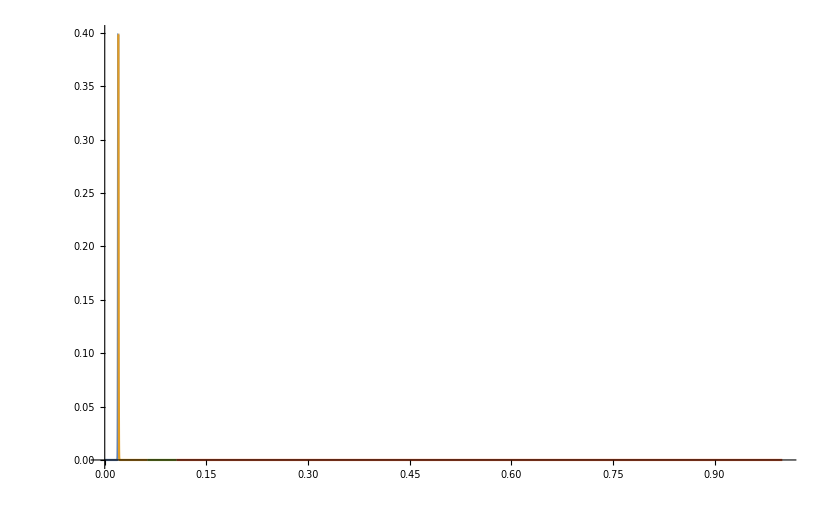

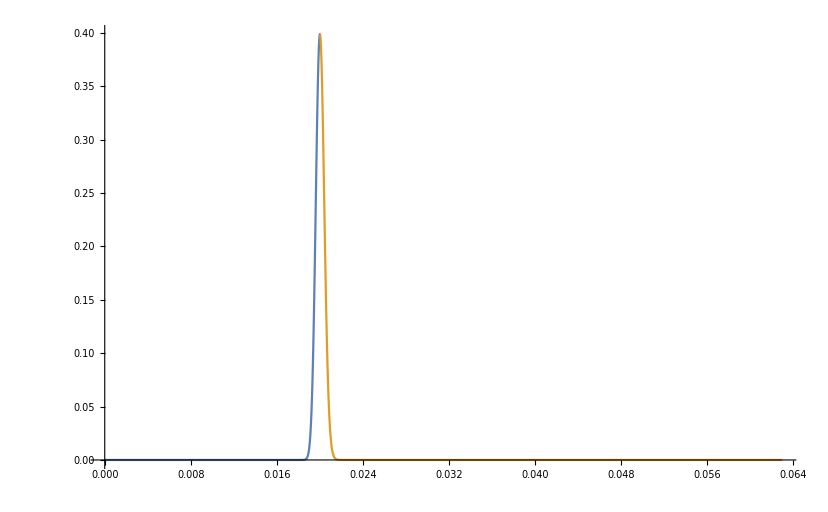

```mathematica
ϕ0Data=Transpose@{z$dom0,ϕ0$dom0};
ϕ1Data=Transpose@{z$dom1,ϕ0$dom1};
ϕ2Data=Transpose@{z$dom2,ϕ0$dom2};
ϕ3Data=Transpose@{z$dom3,ϕ0$dom3};
ListPlot[{ϕ0Data,ϕ1Data,ϕ2Data,ϕ3Data}, Joined->True, PlotRange->All]
ListPlot[{ϕ0Data,ϕ1Data}, Joined->True, PlotRange->All]
```

#### Chebyshev ID

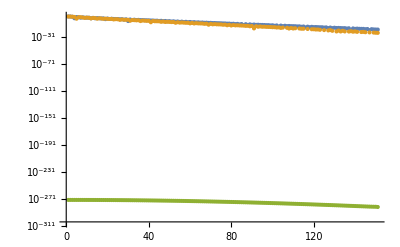

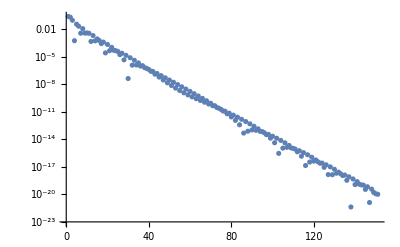

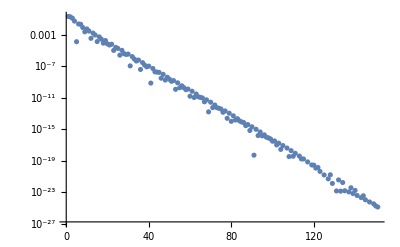

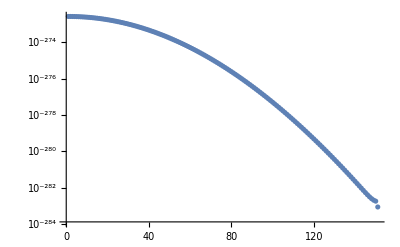

-Graphics-

```mathematica
cϕ0$dom0=ChebLobattoCoefficients[ϕ0$dom0,Prec];
cϕ0$dom1=ChebLobattoCoefficients[ϕ0$dom1,Prec];
cϕ0$dom2=ChebLobattoCoefficients[ϕ0$dom2,Prec];
cϕ0$dom3=ChebLobattoCoefficients[ϕ0$dom3,Prec];

ListLogPlot[{Abs@cϕ0$dom0,Abs@cϕ0$dom1,Abs@cϕ0$dom2,Abs@cϕ0$dom3}]

ListLogPlot[Abs@cϕ0$dom0]
ListLogPlot[Abs@cϕ0$dom1]
ListLogPlot[Abs@cϕ0$dom2]
ListLogPlot[Abs@cϕ0$dom3]
```

### From Operator

#### Source Function ID

```mathematica
(*Bn$dom0=Table[N[B$dom0[s$QNM[[iQNM]],ϕ0$dom0[[iQNM]],ψ0$dom0[[iQNM]]],Prec],{iQNM,1,n$QNM$max}];
Bn$dom1=Table[N[B$dom1[s$QNM[[iQNM]],ϕ0$dom1[[iQNM]],ψ0$dom1[[iQNM]]],Prec],{iQNM,1,n$QNM$max}];
Bn$dom2=Table[N[B$dom2[s$QNM[[iQNM]],ϕ0$dom2[[iQNM]],ψ0$dom2[[iQNM]]],Prec],{iQNM,1,n$QNM$max}];
Bn$dom3=Table[N[B$dom3[s$QNM[[iQNM]],ϕ0$dom3[[iQNM]],ψ0$dom3[[iQNM]]],Prec],{iQNM,1,n$QNM$max}];*)
Bn$dom0=Table[N[B$dom0[s$QNM[[iQNM]],ϕ0$dom0,ψ0$dom0],Prec],{iQNM,1,n$QNM$max}];
Bn$dom1=Table[N[B$dom1[s$QNM[[iQNM]],ϕ0$dom1,ψ0$dom1],Prec],{iQNM,1,n$QNM$max}];
Bn$dom2=Table[N[B$dom2[s$QNM[[iQNM]],ϕ0$dom2,ψ0$dom2],Prec],{iQNM,1,n$QNM$max}];
Bn$dom3=Table[N[B$dom3[s$QNM[[iQNM]],ϕ0$dom3,ψ0$dom3],Prec],{iQNM,1,n$QNM$max}];

Bn=Table[Join[Bn$dom0[[iQNM]],Bn$dom1[[iQNM]],Bn$dom2[[iQNM]],Bn$dom3[[iQNM]]],{iQNM,1,n$QNM$max}];
(*Bn$Conj=Table[B[s$QNM$Conj[[iQNM]],ϕ0,ψ0],{iQNM,1,n$QNM$max}];*)

Bn[[All,1]]=0;
Bn[[All,nz$dom0+1]]=0;
Bn[[All,nz$dom0+nz$dom1]]=0;
Bn[[All,nz$dom0+nz$dom1+1]]=0;
Bn[[All,nz$dom0+nz$dom1+nz$dom2]]=0;
Bn[[All,nz$dom0+nz$dom1+nz$dom2+nz$dom3]]=0;
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating {(-8.49265131998891679571382600593775020766669253145002898701618624133588549808778482689632175412158025012220565347079224177845488503053862595816714336023340768 Power[10, -211] + 4.824753676595<<133>>603215514 <<1>> I) + <<125>>, <<150>>}.

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating {(-8.49265131998891679571382600593775020766669253145002898701618640027494016713074507952073323912239870532296629201686025870867831531868635560129398711816601315 Power[10, -211] + 1.286774536359<<133>>360189483 <<1>> I) + <<125>>, <<150>>}.

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating {(-8.49265131998891679571382600593775020766669253145002898701618650104660384182333272141475143577942941187837354882563403216990133740737140166764534334802757367 Power[10, -211] + 2.187426115662<<133>>265197467 <<1>> I) + <<125>>, <<150>>}.

General::stop: Further output of N::meprec will be suppressed during this calculation.

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating {(-4.9669407743473426509788009313582544511942054112731017091930647285773075259696928921378015237461730329881038344447361260890842571290790221271474062366218853 Power[10, -384] + 3.6090881439500<<132>>939592891 <<1>> I) + <<125>>, <<150>>}.

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating {(-4.9669419632682622811813612453077262613627535912971411741848051335899969412500177701959856831496878464756790932199415052148393697796423895266861685418853122 Power[10, -384] + 9.6255333109365<<131>>624735873 <<1>> I) + <<125>>, <<150>>}.

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating {(-4.9669427170763134128498484956660667956199766076414018012780549281306629936925524947632139216147638401221028143963113309931970190983755044197546600533726333 Power[10, -384] + 1.6362728937023<<132>>745531813 <<1>> I) + <<125>>, <<150>>}.

General::stop: Further output of N::meprec will be suppressed during this calculation.

#### Total Source

```mathematica
g0=1;

S=Table[Append[Bn[[iQNM]] , g0],{iQNM,1,n$QNM$max}];
(*S$Conj=Table[Append[Bn$Conj[[iQNM]] +S2ndOrder$Vec[s$QNM$Conj[[iQNM]]], g0],{iQNM,1,n$QNM$max}];*)
```

#### Amplitude

```mathematica
(*ηSol=Table[MampInv[[iQNM]].S[[iQNM]],{iQNM,1,n$QNM$max}];*)
ηSol=Table[LinearSolve[Mamp[[iQNM]] , S[[iQNM]]] ,{iQNM,1,n$QNM$max}];

η=ηSol[[All,nz$dom0+nz$dom1+nz$dom2+nz$dom3+1]];


ϕScri=ϕQNM$dom0[[All,nz$dom0]];
ϕHrz=ϕQNM$dom1[[All,1]];

ηϕScri=Table[ η[[iQNM]] * ϕScri[[iQNM]],{iQNM,1,n$QNM$max}];
ηϕHrz =Table[ η[[iQNM]] * ϕHrz[[iQNM]],{iQNM,1,n$QNM$max}];

ηϕScri;
Abs[ηϕScri];
```

```mathematica
N@Abs[ηϕScri]
```

{1.94166×10^14,5.62507×10^10,2.93227×10^10,1.62397×10^10,1.0958×10^15,1.20174×10^19,8.98606×10^22,7.0063×10^23,1.43817×10^22}

```mathematica
N@ϕScri
N@η
```

{323.417-149.724 ⅈ,7.69676-28.3337 ⅈ,0.330812-1.68201 ⅈ,0.246531+1.64054 ⅈ,0.289603-0.0596376 ⅈ,0.0144059+0.0643099 ⅈ,-0.0117336-0.00943517 ⅈ,-0.00322182+0.00141778 ⅈ,-0.0000667534+0.0008383 ⅈ}

{5.30687×10^11+1.23239×10^11 ⅈ,1.73218×10^9+8.18604×10^8 ⅈ,-1.39554×10^9+1.70484×10^10 ⅈ,3.79362×10^9+9.02409×10^9 ⅈ,1.29322×10^15-3.47308×10^15 ⅈ,1.79731×10^20-3.07782×10^19 ⅈ,4.04572×10^24+4.38765×10^24 ⅈ,1.06435×10^26+1.68196×10^26 ⅈ,-1.52826×10^25-7.67521×10^24 ⅈ}

```mathematica
N@S[[1]]
```

General::munfl: -1.1217682427991159210472651834332834955943968301519808287672018180057373221932564057708493295661917226630387679276622568055730973522058139966748606×10^-279+3.64671181210275978788952352004237733306307643326211106335516916249849586823957775078837979882531760153821913259358314088086559024185412816045270185807643×10^-390 ⅈ is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.1221322146411958378701286583392493040362849550807104908896884927711962044656942027173090811848987375869717144897340579005819793752936817353491769×10^-279+3.76194428441019148339717808532613040365857501511510512048476678912547368864395036022405897118247815555590492760550488207048257845924565421158936384340644×10^-390 ⅈ is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -1.1227379861674475316313171304680748640206312783615700392144787787276686714817671175212714203991150475431041874660479585398867362037330365178677582×10^-279+3.96211795756147380175162732513882100942508436739750569327531281682411419392583666451072664378882498442508536482685064991296637581233324259500716991118609×10^-390 ⅈ is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{0.,1.23071+0.264347 ⅈ,3.5308+0.264346 ⅈ,7.36382+0.264345 ⅈ,12.7291+0.264341 ⅈ,19.6255+0.264334 ⅈ,28.0517+0.264321 ⅈ,38.0059+0.2643 ⅈ,49.4858+0.264268 ⅈ,62.4884+0.264221 ⅈ,77.0103+0.264156 ⅈ,93.0473+0.264069 ⅈ,110.594+0.263955 ⅈ,129.644+0.263808 ⅈ,150.191+0.263624 ⅈ,172.226+0.263397 ⅈ,195.738+0.263119 ⅈ,220.715+0.262785 ⅈ,247.144+0.262387 ⅈ,275.007+0.261917 ⅈ,304.285+0.261366 ⅈ,334.956+0.260727 ⅈ,366.993+0.259989 ⅈ,400.364+0.259143 ⅈ,435.033+0.258178 ⅈ,470.956+0.257082 ⅈ,508.083+0.255844 ⅈ,546.355+0.25445 ⅈ,585.701+0.252888 ⅈ,626.038+0.251142 ⅈ,667.27+0.249198 ⅈ,709.284+0.247038 ⅈ,751.946+0.244647 ⅈ,795.1+0.242005 ⅈ,838.565+0.239094 ⅈ,882.129+0.235893 ⅈ,925.548+0.232383 ⅈ,968.537+0.228542 ⅈ,1010.77+0.224348 ⅈ,1051.88+0.21978 ⅈ,1091.43+0.214815 ⅈ,1128.95+0.209434 ⅈ,1163.91+0.203617 ⅈ,1195.71+0.197346 ⅈ,1223.68+0.190608 ⅈ,1247.13+0.183392 ⅈ,1265.29+0.175694 ⅈ,1277.37+0.167515 ⅈ,1282.54+0.158867 ⅈ,1280.+0.14977 ⅈ,1268.95+0.140256 ⅈ,1248.7+0.130372 ⅈ,1218.67+0.120178 ⅈ,1178.44+0.109753 ⅈ,1127.86+0.0991903 ⅈ,1067.08+0.0886 ⅈ,996.614+0.0781077 ⅈ,917.418+0.0678505 ⅈ,830.894+0.0579734 ⅈ,738.911+0.0486226 ⅈ,643.758+0.0399379 ⅈ,548.058+0.0320441 ⅈ,454.621+0.0250415 ⅈ,366.247+0.0189975 ⅈ,285.496+0.0139394 ⅈ,214.447+0.00985113 ⅈ,154.487+0.00667378 ⅈ,106.172+0.00431107 ⅈ,69.1938+0.00263943 ⅈ,42.4738+0.00152122 ⅈ,24.3693+0.000819025 ⅈ,12.956+0.000408367 ⅈ,6.32054+0.000186719 ⅈ,2.79819+0.0000774266 ⅈ,1.1102+0.0000287543 ⅈ,0.389193+9.42874×10^-6 ⅈ,0.11863+2.68633×10^-6 ⅈ,0.0308743+6.52998×10^-7 ⅈ,0.0067208+1.32662×10^-7 ⅈ,0.00119544+2.20046×10^-8 ⅈ,0.000169205+2.90197×10^-9 ⅈ,0.0000184939+2.95271×10^-10 ⅈ,1.50856×10^-6+2.2401×10^-11 ⅈ,8.83451×10^-8+1.21895×10^-12 ⅈ,3.55434×10^-9+4.55224×10^-14 ⅈ,9.34369×10^-11+1.1097×10^-15 ⅈ,1.51847×10^-12+1.66775×10^-17 ⅈ,1.1898×10^-14+1.44794×10^-19 ⅈ,2.30146×10^-15+6.7429×10^-22 ⅈ,-2.11334×10^-15+1.54756×10^-24 ⅈ,1.98591×10^-15+1.58903×10^-27 ⅈ,-1.85256×10^-15+6.53475×10^-31 ⅈ,1.71821×10^-15+9.48169×10^-35 ⅈ,-1.58653×10^-15+4.19725×10^-39 ⅈ,1.46018×10^-15+4.79693×10^-44 ⅈ,-1.34087×10^-15+1.16816×10^-49 ⅈ,1.2296×10^-15+4.8589×10^-56 ⅈ,-1.12679×10^-15+2.67467×10^-63 ⅈ,1.03245×10^-15+1.45089×10^-71 ⅈ,-9.46324×10^-16+5.51247×10^-81 ⅈ,8.67992×10^-16+9.87095×10^-92 ⅈ,-7.96929×10^-16+5.25586×10^-104 ⅈ,7.32568×10^-16+4.86535×10^-118 ⅈ,-6.74335×10^-16+4.18333×10^-134 ⅈ,6.21669×10^-16+1.60355×10^-152 ⅈ,-5.74041×10^-16+1.15752×10^-173 ⅈ,5.30956×10^-16+0. ⅈ,-4.9196×10^-16+0. ⅈ,4.5664×10^-16+0. ⅈ,-4.24622×10^-16+0. ⅈ,3.9557×10^-16+0. ⅈ,-3.69182×10^-16+0. ⅈ,3.45189×10^-16+0. ⅈ,-3.2335×10^-16+0. ⅈ,3.0345×10^-16+0. ⅈ,-2.85297×10^-16+0. ⅈ,2.68722×10^-16+0. ⅈ,-2.53571×10^-16+0. ⅈ,2.39708×10^-16+0. ⅈ,-2.27014×10^-16+0. ⅈ,2.15378×10^-16+0. ⅈ,-2.04705×10^-16+0. ⅈ,1.94908×10^-16+0. ⅈ,-1.8591×10^-16+0. ⅈ,1.77641×10^-16+0. ⅈ,-1.70039×10^-16+0. ⅈ,1.63048×10^-16+0. ⅈ,-1.56618×10^-16+0. ⅈ,1.50705×10^-16+0. ⅈ,-1.45267×10^-16+0. ⅈ,1.40268×10^-16+0. ⅈ,-1.35675×10^-16+0. ⅈ,1.3146×10^-16+0. ⅈ,-1.27595×10^-16+0. ⅈ,1.24057×10^-16+0. ⅈ,-1.20824×10^-16+0. ⅈ,1.17877×10^-16+0. ⅈ,-1.15199×10^-16+0. ⅈ,1.12774×10^-16+0. ⅈ,-1.10589×10^-16+0. ⅈ,1.08632×10^-16+0. ⅈ,-1.06891×10^-16+0. ⅈ,1.05358×10^-16+0. ⅈ,-1.04023×10^-16+0. ⅈ,1.0288×10^-16+0. ⅈ,-1.01923×10^-16+0. ⅈ,1.01147×10^-16+0. ⅈ,-1.00547×10^-16+0. ⅈ,1.00121×10^-16+0. ⅈ,-9.98662×10^-17+0. ⅈ,1.99563×10^-16,0.,-1.08904×10^-22+6.03554×10^-272 ⅈ,1.08999×10^-22+1.18139×10^-271 ⅈ,-1.09157×10^-22+3.61715×10^-271 ⅈ,1.09376×10^-22+1.73144×10^-270 ⅈ,-1.09656×10^-22+1.29474×10^-269 ⅈ,1.09995×10^-22+1.51094×10^-268 ⅈ,-1.10389×10^-22+2.74822×10^-267 ⅈ,1.10837×10^-22+7.77872×10^-266 ⅈ,-1.11334×10^-22+3.41974×10^-264 ⅈ,1.11877×10^-22+2.32984×10^-262 ⅈ,-1.1246×10^-22+2.45334×10^-260 ⅈ,1.13078×10^-22+3.98057×10^-258 ⅈ,-1.13722×10^-22+9.91596×10^-256 ⅈ,1.14385×10^-22+3.77697×10^-253 ⅈ,-1.15057×10^-22+2.18943×10^-250 ⅈ,1.15726×10^-22+1.92124×10^-247 ⅈ,-1.16379×10^-22+2.53673×10^-244 ⅈ,1.17×10^-22+5.00562×10^-241 ⅈ,-1.17571×10^-22+1.46497×10^-237 ⅈ,1.18071×10^-22+6.30521×10^-234 ⅈ,-1.18474×10^-22+3.95349×10^-230 ⅈ,1.18752×10^-22+3.57394×10^-226 ⅈ,-1.18871×10^-22+4.60493×10^-222 ⅈ,1.18793×10^-22+8.35128×10^-218 ⅈ,-1.18472×10^-22+2.10274×10^-213 ⅈ,1.17856×10^-22+7.24201×10^-209 ⅈ,-1.16883×10^-22+3.35725×10^-204 ⅈ,1.15484×10^-22+2.05888×10^-199 ⅈ,-1.13574×10^-22+1.63961×10^-194 ⅈ,1.1106×10^-22+1.66228×10^-189 ⅈ,-1.0783×10^-22+2.10079×10^-184 ⅈ,1.03755×10^-22+3.23684×10^-179 ⅈ,-9.86866×10^-23+5.93962×10^-174 ⅈ,9.24504×10^-23+1.26667×10^-168 ⅈ,-8.48448×10^-23+3.06029×10^-163 ⅈ,7.56354×10^-23+8.15811×10^-158 ⅈ,-6.45498×10^-23+2.33522×10^-152 ⅈ,5.12711×10^-23+6.98025×10^-147 ⅈ,-3.54311×10^-23+2.11783×10^-141 ⅈ,1.66015×10^-23+6.33728×10^-136 ⅈ,5.71595×10^-24+1.81698×10^-130 ⅈ,-3.21008×10^-23+4.8493×10^-125 ⅈ,6.32273×10^-23+1.17067×10^-119 ⅈ,-9.98795×10^-23+2.48512×10^-114 ⅈ,1.42969×10^-22+4.51253×10^-109 ⅈ,-1.93557×10^-22+6.82386×10^-104 ⅈ,2.52875×10^-22+8.37548×10^-99 ⅈ,-3.22353×10^-22+8.14218×10^-94 ⅈ,4.03651×10^-22+6.12682×10^-89 ⅈ,-4.9869×10^-22+3.4931×10^-84 ⅈ,6.09691×10^-22+1.47967×10^-79 ⅈ,-7.39219×10^-22+4.57533×10^-75 ⅈ,8.90222×10^-22+1.01673×10^-70 ⅈ,-1.06608×10^-21+1.60196×10^-66 ⅈ,1.27065×10^-21+1.76952×10^-62 ⅈ,-1.5083×10^-21+1.35795×10^-58 ⅈ,1.78396×10^-21+7.19055×10^-55 ⅈ,-2.10315×10^-21+2.61509×10^-51 ⅈ,2.47195×10^-21+6.51613×10^-48 ⅈ,-2.89699×10^-21+1.11202×10^-44 ⅈ,3.3854×10^-21+1.30187×10^-41 ⅈ,-3.94463×10^-21+1.04925×10^-38 ⅈ,4.58233×10^-21+5.85234×10^-36 ⅈ,-5.30598×10^-21+2.27457×10^-33 ⅈ,6.12256×10^-21+6.21145×10^-31 ⅈ,-7.0445×10^-21+1.20328×10^-28 ⅈ,7.19429×10^-21+1.67132×10^-26 ⅈ,-9.44096×10^-20+1.6839×10^-24 ⅈ,-6.1628×10^-18+1.24596×10^-22 ⅈ,-3.32231×10^-16+6.85905×10^-21 ⅈ,-1.34636×10^-14+2.84721×10^-19 ⅈ,-4.16575×10^-13+9.03491×10^-18 ⅈ,-9.97829×10^-12+2.22227×10^-16 ⅈ,-1.8763×10^-10+4.29608×10^-15 ⅈ,-2.80829×10^-9+6.61827×10^-14 ⅈ,-3.39164×10^-8+8.23616×10^-13 ⅈ,-3.34979×10^-7+8.39087×10^-12 ⅈ,-2.74108×10^-6+7.08975×10^-11 ⅈ,-0.0000188193+5.03102×10^-10 ⅈ,-0.000109733+3.03487×10^-9 ⅈ,-0.000549769+1.57442×10^-8 ⅈ,-0.00239307+7.10235×10^-8 ⅈ,-0.00914631+2.81545×10^-7 ⅈ,-0.0310016+9.90554×10^-7 ⅈ,-0.0940714+3.12219×10^-6 ⅈ,-0.257813+8.8944×10^-6 ⅈ,-0.643453+0.0000230902 ⅈ,-1.47384+0.0000550468 ⅈ,-3.12053+0.000121378 ⅈ,-6.14818+0.000249196 ⅈ,-11.342+0.000479296 ⅈ,-19.7032+0.000868561 ⅈ,-32.4021+0.00149076 ⅈ,-50.6871+0.00243511 ⅈ,-75.7601+0.00380241 ⅈ,-108.635+0.0056989 ⅈ,-150.002+0.00822869 ⅈ,-200.126+0.0114855 ⅈ,-258.78+0.0155454 ⅈ,-325.239+0.02046 ⅈ,-398.318+0.0262532 ⅈ,-476.457+0.0329191 ⅈ,-557.823+0.0404227 ⅈ,-640.436+0.0487026 ⅈ,-722.284+0.0576751 ⅈ,-801.434+0.0672394 ⅈ,-876.113+0.0772826 ⅈ,-944.781+0.0876856 ⅈ,-1006.17+0.0983275 ⅈ,-1059.29+0.10909 ⅈ,-1103.46+0.11986 ⅈ,-1138.26+0.130535 ⅈ,-1163.55+0.141021 ⅈ,-1179.39+0.151237 ⅈ,-1186.03+0.161111 ⅈ,-1183.91+0.170586 ⅈ,-1173.55+0.179616 ⅈ,-1155.6+0.188165 ⅈ,-1130.76+0.196207 ⅈ,-1099.75+0.203726 ⅈ,-1063.34+0.210714 ⅈ,-1022.29+0.21717 ⅈ,-977.35+0.223099 ⅈ,-929.236+0.228512 ⅈ,-878.644+0.233423 ⅈ,-826.226+0.237851 ⅈ,-772.596+0.241818 ⅈ,-718.32+0.245348 ⅈ,-663.919+0.248467 ⅈ,-609.867+0.251201 ⅈ,-556.594+0.253579 ⅈ,-504.481+0.255629 ⅈ,-453.871+0.257379 ⅈ,-405.064+0.258856 ⅈ,-358.322+0.26009 ⅈ,-313.872+0.261107 ⅈ,-271.909+0.261931 ⅈ,-232.596+0.26259 ⅈ,-196.073+0.263104 ⅈ,-162.455+0.263497 ⅈ,-131.834+0.26379 ⅈ,-104.287+0.263999 ⅈ,-79.874+0.264144 ⅈ,-58.6419+0.264238 ⅈ,-40.6271+0.264295 ⅈ,-25.8568+0.264326 ⅈ,-14.3509+0.264341 ⅈ,-6.12327+0.264346 ⅈ,-1.18326+0.264347 ⅈ,0.,0.,-1.12177×10^-279+0. ⅈ,1.12213×10^-279+0. ⅈ,-1.12274×10^-279+0. ⅈ,1.12358×10^-279+0. ⅈ,-1.12467×10^-279+0. ⅈ,1.12599×10^-279+0. ⅈ,-1.12755×10^-279+0. ⅈ,1.12933×10^-279+0. ⅈ,-1.13134×10^-279+0. ⅈ,1.13358×10^-279+0. ⅈ,-1.13603×10^-279+0. ⅈ,1.13869×10^-279+0. ⅈ,-1.14156×10^-279+0. ⅈ,1.14463×10^-279+0. ⅈ,-1.14789×10^-279+0. ⅈ,1.15134×10^-279+0. ⅈ,-1.15496×10^-279+0. ⅈ,1.15875×10^-279+0. ⅈ,-1.16271×10^-279+0. ⅈ,1.16681×10^-279+0. ⅈ,-1.17105×10^-279+0. ⅈ,1.17543×10^-279+0. ⅈ,-1.17992×10^-279+0. ⅈ,1.18452×10^-279+0. ⅈ,-1.18922×10^-279+0. ⅈ,1.19401×10^-279+0. ⅈ,-1.19887×10^-279+0. ⅈ,1.20379×10^-279+0. ⅈ,-1.20876×10^-279+0. ⅈ,1.21376×10^-279+0. ⅈ,-1.2188×10^-279+0. ⅈ,1.22384×10^-279+0. ⅈ,-1.22888×10^-279+0. ⅈ,1.23391×10^-279+0. ⅈ,-1.23891×10^-279+0. ⅈ,1.24387×10^-279+0. ⅈ,-1.24879×10^-279+0. ⅈ,1.25364×10^-279+0. ⅈ,-1.25843×10^-279+0. ⅈ,1.26313×10^-279+0. ⅈ,-1.26774×10^-279+0. ⅈ,1.27225×10^-279+0. ⅈ,-1.27666×10^-279+0. ⅈ,1.28095×10^-279+0. ⅈ,-1.28513×10^-279+0. ⅈ,1.28917×10^-279+0. ⅈ,-1.29309×10^-279+0. ⅈ,1.29688×10^-279+0. ⅈ,-1.30054×10^-279+0. ⅈ,1.30406×10^-279+0. ⅈ,-1.30745×10^-279+0. ⅈ,1.31071×10^-279+0. ⅈ,-1.31384×10^-279+0. ⅈ,1.31685×10^-279+0. ⅈ,-1.31975×10^-279+0. ⅈ,1.32254×10^-279+0. ⅈ,-1.32524×10^-279+0. ⅈ,1.32784×10^-279+0. ⅈ,-1.33037×10^-279+0. ⅈ,1.33284×10^-279+0. ⅈ,-1.33526×10^-279+0. ⅈ,1.33764×10^-279+0. ⅈ,-1.34001×10^-279+0. ⅈ,1.34239×10^-279+0. ⅈ,-1.34478×10^-279+0. ⅈ,1.34722×10^-279+0. ⅈ,-1.34972×10^-279+0. ⅈ,1.35231×10^-279+0. ⅈ,-1.35501×10^-279+0. ⅈ,1.35784×10^-279+0. ⅈ,-1.36084×10^-279+0. ⅈ,1.36402×10^-279+0. ⅈ,-1.36742×10^-279+0. ⅈ,1.37107×10^-279+0. ⅈ,-1.37499×10^-279+0. ⅈ,1.37922×10^-279+0. ⅈ,-1.38379×10^-279+0. ⅈ,1.38873×10^-279+0. ⅈ,-1.39408×10^-279+0. ⅈ,1.39987×10^-279+0. ⅈ,-1.40615×10^-279+0. ⅈ,1.41294×10^-279+0. ⅈ,-1.4203×10^-279+0. ⅈ,1.42827×10^-279+0. ⅈ,-1.43688×10^-279+0. ⅈ,1.44619×10^-279+0. ⅈ,-1.45624×10^-279+0. ⅈ,1.46709×10^-279+0. ⅈ,-1.47879×10^-279+0. ⅈ,1.4914×10^-279+0. ⅈ,-1.50498×10^-279+0. ⅈ,1.5196×10^-279+0. ⅈ,-1.53531×10^-279+0. ⅈ,1.55221×10^-279+0. ⅈ,-1.57035×10^-279+0. ⅈ,1.58984×10^-279+0. ⅈ,-1.61075×10^-279+0. ⅈ,1.63319×10^-279+0. ⅈ,-1.65726×10^-279+0. ⅈ,1.68306×10^-279+0. ⅈ,-1.71073×10^-279+0. ⅈ,1.74039×10^-279+0. ⅈ,-1.77218×10^-279+0. ⅈ,1.80626×10^-279+0. ⅈ,-1.84279×10^-279+0. ⅈ,1.88196×10^-279+0. ⅈ,-1.92397×10^-279+1.×10^-323 ⅈ,1.96903×10^-279+4.25×10^-322 ⅈ,-2.01738×10^-279+1.6734×10^-320 ⅈ,2.06928×10^-279+6.7664×10^-319 ⅈ,-2.12501×10^-279+2.80906×10^-317 ⅈ,2.18489×10^-279+1.1927×10^-315 ⅈ,-2.24925×10^-279+5.15818×10^-314 ⅈ,2.31847×10^-279+2.26241×10^-312 ⅈ,-2.39297×10^-279+1.00173×10^-310 ⅈ,2.4732×10^-279+4.45553×10^-309 ⅈ,-2.55966×10^-279+1.98051×10^-307 ⅈ,2.65289×10^-279+8.75017×10^-306 ⅈ,-2.75349×10^-279+3.82067×10^-304 ⅈ,2.86214×10^-279+1.63891×10^-302 ⅈ,-2.97955×10^-279+6.86384×10^-301 ⅈ,3.10652×10^-279+2.7885×10^-299 ⅈ,-3.24392×10^-279+1.09162×10^-297 ⅈ,3.39269×10^-279+4.08963×10^-296 ⅈ,-3.55386×10^-279+1.45594×10^-294 ⅈ,3.72853×10^-279+4.89×10^-293 ⅈ,-3.91788×10^-279+1.53811×10^-291 ⅈ,4.12315×10^-279+4.4971×10^-290 ⅈ,-4.34569×10^-279+1.213×10^-288 ⅈ,4.58598×10^-279+2.99551×10^-287 ⅈ,-4.86455×10^-279+6.72124×10^-286 ⅈ,4.78542×10^-279+1.35985×10^-284 ⅈ,-1.1717×10^-278+2.46216×10^-283 ⅈ,-9.60325×10^-278+3.9599×10^-282 ⅈ,-1.45987×10^-276+5.61581×10^-281 ⅈ,-1.81633×10^-275+6.9726×10^-280 ⅈ,-1.97376×10^-274+7.5269×10^-279 ⅈ,-1.85083×10^-273+7.01738×10^-278 ⅈ,-1.48882×10^-272+5.61433×10^-277 ⅈ,-1.02109×10^-271+3.8314×10^-276 ⅈ,-5.93705×10^-271+2.21763×10^-275 ⅈ,-2.91118×10^-270+1.08296×10^-274 ⅈ,-1.19803×10^-269+4.44051×10^-274 ⅈ,-4.11989×10^-269+1.52221×10^-273 ⅈ,-1.1794×10^-268+4.3459×10^-273 ⅈ,-2.80134×10^-268+1.02997×10^-272 ⅈ,-5.50582×10^-268+2.02085×10^-272 ⅈ,-8.93517×10^-268+3.2755×10^-272 ⅈ,-1.19547×10^-267+4.37918×10^-272 ⅈ,0.,0.,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.,1.}

```mathematica
ηSol=Table[MampInv[[iQNM]].S[[iQNM]],{iQNM,1,n$QNM$max}];
```

```mathematica
η=ηSol[[All,nz$dom0+nz$dom1+nz$dom2+nz$dom3+1]];
```

```mathematica
N[η]
```

{5.30687×10^11+1.23239×10^11 ⅈ,1.73218×10^9+8.18604×10^8 ⅈ,-1.39554×10^9+1.70484×10^10 ⅈ,3.79362×10^9+9.02409×10^9 ⅈ,1.29322×10^15-3.47308×10^15 ⅈ,1.79731×10^20-3.07782×10^19 ⅈ,4.04572×10^24+4.38765×10^24 ⅈ,1.06435×10^26+1.68196×10^26 ⅈ,-1.52826×10^25-7.67521×10^24 ⅈ}

```mathematica
N[s$QNM]
N[ηϕScri]
N[Abs[ηϕScri]]
N[Arg[ηϕScri]]
```

{-0.304656-0.162407 ⅈ,-0.251156-0.433143 ⅈ,-0.217235-0.736313 ⅈ,-0.211645+0.739198 ⅈ,-0.36968+0.971584 ⅈ,-0.480186-1.18411 ⅈ,-0.588012+1.40296 ⅈ,-0.693698+1.62596 ⅈ,-0.797748+1.85165 ⅈ}

{-0.0217714-0.00525891 ⅈ,-0.0414597+0.00241274 ⅈ,-5.58267+6.12056 ⅈ,5.89392+6.39754 ⅈ,0.0517134-0.158442 ⅈ,-0.000972317+0.0953877 ⅈ,-0.0123802-0.0616709 ⅈ,-0.0138938-0.0440568 ⅈ,-0.0134338-0.034155 ⅈ}

{0.0223975,0.0415299,8.28417,8.69866,0.166668,0.0953927,0.0629013,0.0461956,0.0367019}

{-2.90458,3.08346,2.31027,0.826349,-1.25531,1.58099,-1.76891,-1.87628,-1.94553}

### From Kaldesh

#### Initial Data Vector

```mathematica
ϕID=Join[Reverse@ϕ0$dom0,Reverse@ϕ0$dom1,Reverse@ϕ0$dom2,Reverse@ϕ0$dom3];
ψID=Join[Reverse@ψ0$dom0,Reverse@ψ0$dom1,Reverse@ψ0$dom2,Reverse@ψ0$dom3];

uID=Join[ϕID,ψID];
```

#### Amplitude

```mathematica
ηK=Table[ut[[iQNM]].uID,{iQNM,1,n$QNM$max}];
N[ηK]
```

{-0.00112571-0.00217847 ⅈ,-0.0411453+0.00969504 ⅈ,0.475381+0.531009 ⅈ,0.234048-0.174776 ⅈ,0.922387-1.09548 ⅈ,0.1781-0.264089 ⅈ,0.595506+6.57759 ⅈ,-4.04074-8.44825 ⅈ,2.73025+2.89577 ⅈ}

```mathematica
s0=s$QNM[[4]]
ρ0=Abs[ηϕScri[[4]]]
ϕ0=Arg[ηϕScri[[4]]]
```

-0.2116451411183049057706762106223635572534131234672284606286025965653913979630384882473688118595513078748405290413293350380061205163470414047391215176122135+0.7391984327078456282195297917706771093215200019673262304849934541529971861748869748028918141738568964871713679212111365145396862659936367728508555460240967 ⅈ

1.37169507130595783132360189356879228967733662295455528726010320789374585798789778241480804503142085377930115424953447350287392932919426×10^10

3.06342925044745059536650884908765213903530636959891910395840784642553039530647472281348294144571187221324572572629379780675839726835839

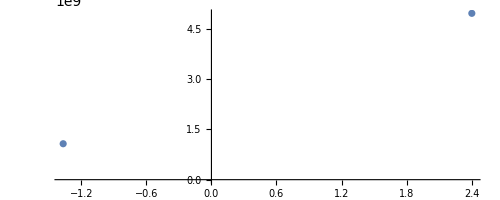

```mathematica
ComplexListPlot[{ηϕScri[[4]],Conjugate@ηϕScri[[3]]}]
```

```mathematica
s1=Conjugate[s$QNM[[3]]]
ρ1=Abs[Conjugate[ηϕScri[[3]]]]
ϕ1=Arg[Conjugate[ηϕScri[[3]]]]

(*s1=s$QNM[[4]]
ρ1=Abs[ηϕScri[[4]]]
ϕ1=Arg[ηϕScri[[4]]]*)
```

-0.21723470956908508137851908612804350326402796729166612897067857265210366656153883527939279900118278952027687944910756612245175749857976432123882332713421202+0.7363125540671859417784672389040264754426714684417051197621817949455621927485636955146665400221693758446440700016625869127878744275564348138051270672608214 ⅈ

2.45217581385521606983408381272838362488376427520934400712041788201462121142579725471533613243091670689759383988036072588947619919050497×10^10

0.2035857790943884326340929899299522709504307080278083791522575578777586911606213408916116363182318219860127166534742411737283192279915

```mathematica
δs=s1-s0
δsR=Re[δs]
δsI=Im[δs]
δρ=ρ1-ρ0
δϕ=ϕ0-ϕ1-π
 
 sR=-Re[s0];
 sI=Im[s0];
```

-0.00558956845078017560784287550567994601061484382443766834207597608671226859850034703202398714163148164543635040777823108444563698223272291649970180952199852-0.0028858786406596864410625528666506338788485335256211107228116592074349934263232792882252741516875206425272979195485496017518118384372019590457284787632754 ⅈ

-0.00558956845078017560784287550567994601061484382443766834207597608671226859850034703202398714163148164543635040777823108444563698223272291649970180952199852

-0.0028858786406596864410625528666506338788485335256211107228116592074349934263232792882252741516875206425272979195485496017518118384372019590457284787632754

1.0804807425492582385104819191595913352064276522547887198603146741208753534378994723005280873994958531182926856308262523866022698613107×10^10

-0.28174918223673107573022752412180301611229373780399509616879430376004470214035561670616352021463701775491507744046275001406376656918369

Dependence of ηϕScri on (ϵ,ao)

```mathematica
(*ηSol$Conj=Table[Mamp$ConjInv[[iQNM]].S$Conj[[iQNM]],{iQNM,1,n$QNM$max}];
η$Conj=ηSol$Conj[[All,Nz+2]];
ϕScri$Conj=ϕQNM$Conj$Vec[[All,nz]];
ϕHrz$Conj=ϕQNM$Conj$Vec[[All,1]];

ηϕScri$Conj=Table[η$Conj[[iQNM]]*ϕScri$Conj[[iQNM]],{iQNM,1,n$QNM$max}];
ηϕHrz$Conj=Table[η$Conj[[iQNM]]*ϕHrz$Conj[[iQNM]],{iQNM,1,n$QNM$max}];

Abs[ηϕScri$Conj]
Abs[ηϕHrz$Conj]*)
```

## Comparison Against Time Evolution

## Exact QNMs Contributions

```mathematica
hQNM$Scri[τ_, n_]:= 2*Re[ ηϕScri[[n]]*Exp[s$QNM[[n]]*τ]] (*+ ηϕScri$Conj[[n+1]]*Exp[s$QNM$Conj[[n+1]]*τ];*)
hQNM$Hrz[τ_, n_]:= 2* Re[ηϕHrz[[n]]*Exp[s$QNM[[n]]*τ]](* + ηϕHrz$Conj[[n+1]]*Exp[s$QNM$Conj[[n+1]]*τ];*)



PlotFreqEvol = Table[ LogPlot[Abs@hQNM$Scri[τ,iQNM], {τ,0,100}, WorkingPrecision->100, PlotLabels->{"sQNM_"<>ToString[iQNM-1]}, PlotStyle->ColorData[iQNM,"ColorList"], PlotRange->All], {iQNM, 1,n$QNM$max }];

Show[PlotFreqEvol]
```

-Graphics-

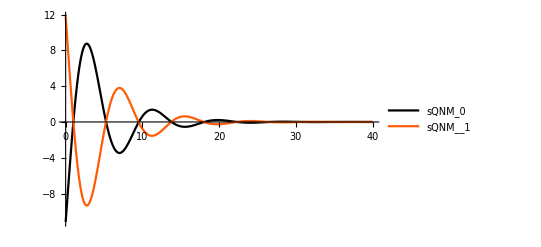

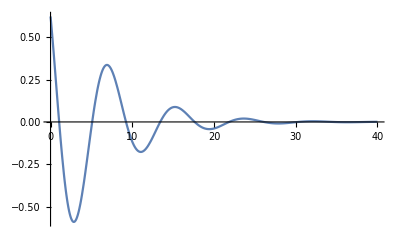

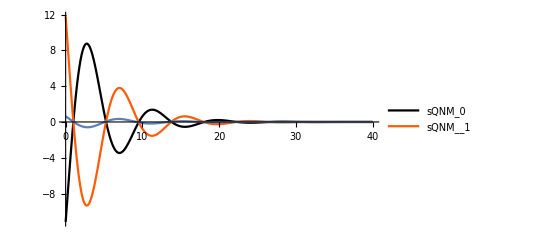

```mathematica
PlotFreqEvol =  Plot[{hQNM$Scri[τ,3],hQNM$Scri[τ,4]}, {τ,0,40}, WorkingPrecision->100, PlotLegends->{{"sQNM_0","sQNM__1"}}, PlotStyle->ColorData[3,"ColorList"], PlotRange->All]
PlotFreqEvolSum =  Plot[hQNM$Scri[τ,3]+hQNM$Scri[τ,4], {τ,0,40}, WorkingPrecision->100,  PlotRange->All]

Show[PlotFreqEvol,PlotFreqEvolSum]
```

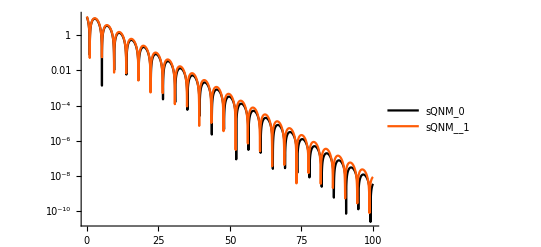

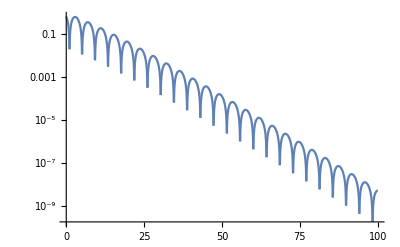

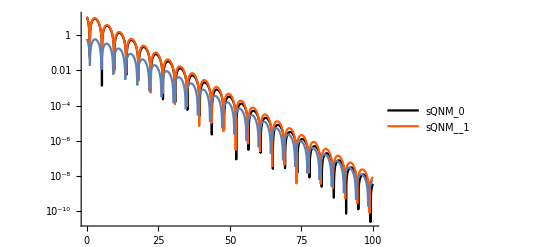

```mathematica
PlotFreqEvol =  LogPlot[{Abs@hQNM$Scri[τ,3],Abs@hQNM$Scri[τ,4]}, {τ,0,100}, WorkingPrecision->100, PlotLegends->{{"sQNM_0","sQNM__1"}}, PlotStyle->ColorData[3,"ColorList"], PlotRange->All]
PlotFreqEvolSum =  LogPlot[Abs[hQNM$Scri[τ,3]+hQNM$Scri[τ,4]], {τ,0,100}, WorkingPrecision->100,  PlotRange->All]

Show[PlotFreqEvol,PlotFreqEvolSum]
```

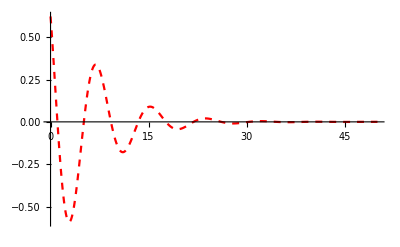

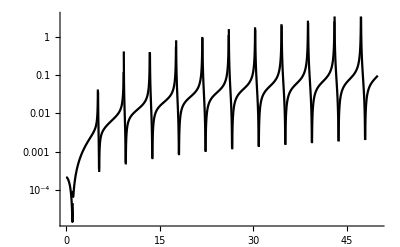

-Graphics-

```mathematica
h$Interference=-2*(ⅇ^(-sR τ) (δρ (1+δsR τ) (1+δsI δϕ τ)+ρ0 τ (δsR+δsI δϕ+δsI δsR δϕ τ)) Cos[sI τ+ϕ0]+ⅇ^(-sR τ) (δρ+ρ0) (δϕ-δsI τ) (1+δsR τ) Sin[sI τ+ϕ0]);
PlotInterference=Plot[h$Interference,{τ,0,50}, PlotStyle->{Red,Dashed}, PlotRange->All]
InterferenceError=Abs[1-h$Interference/(hQNM$Scri[τ,3]+hQNM$Scri[τ,4])];
PlotError=LogPlot[InterferenceError,{τ,0,50}, PlotStyle->{Black}, PlotRange->All]
Show[PlotFreqEvol,PlotInterference]
```

## Load Time Evolution Data

```mathematica
Print["Load data"];

n$QNM$FirstOrder=0;
WaveDataFile=DirName<>"../data/CteField/spin_"<>ToString[spin]<>"/l_"<>ToString[l]<>"/epsilon_"<>ToString[NumberForm[N[ϵ],{7,6},NumberPadding->{"","0"}]]<>"_a0_"<>ToString[NumberForm[N[ao],{7,6},NumberPadding->{"","0"}]]<>"/N0_5_N1_100_ndom_4_nfields_2/gnuplot2D_field_0_dom_0.dat"
WaveDataRaw1=Import[WaveDataFile, "Table"];

WaveDataHeader1=WaveDataRaw1[[1]]
WaveData1=Delete[WaveDataRaw1,1];
NWave=Length@WaveData1
Time=WaveData1[[All,1]];
h=Time[[2]]-Time[[1]]
hScri=WaveData1[[All,2]];
hHrz=WaveData1[[All,22]];

hQNM$Hrz$ExactData=.
hQNM$Hrz$ExactData[n_]:=hQNM$Hrz[Time,n+1];


hQNM$Scri$ExactData=.
hQNM$Scri$ExactData[n_]:=hQNM$Scri[Time,n+1];
```

Load data

/Users/qtc325/Trabalhos/NBIA/2024_09_QNMResonantExcitation_ElephantFlea/SphericalSym_ElephFlea_TimeEvol/ExternalCodes/../data/CteField/spin_2/l_2/epsilon_0.002040_a0_11.572200/N0_5_N1_100_ndom_4_nfields_2/gnuplot2D_field_0_dom_0.dat

{#1:T,#2:0.000e+00,#3:4.424e-03,#4:7.870e-03,#5:1.055e-02,#6:1.264e-02,#7:1.427e-02,#8:1.554e-02,#9:1.653e-02,#10:1.730e-02,#11:1.790e-02,#12:1.837e-02,#13:1.874e-02,#14:1.902e-02,#15:1.925e-02,#16:1.943e-02,#17:1.957e-02,#18:1.968e-02,#19:1.978e-02,#20:1.986e-02,#21:1.993e-02,#22:2.000e-02}

5001

0.1

#### Map time to index

```mathematica
ti=Time[[1]]
tf=Time[[NWave]]
δt=tf-ti

IndxT[t_]:=Round[(NWave-1)*(t-ti)/δt+1 ];
```

0.

500.

500.

## Filtering QNM

Plot data

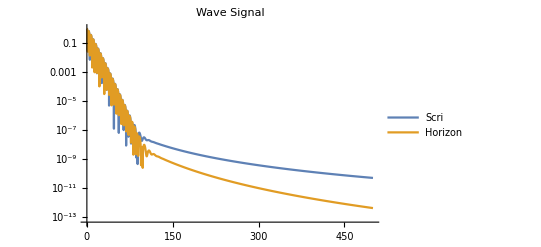

```mathematica
Print["Plot data"];
PlotWave=ListLogPlot[
{Transpose@{Time,Abs@hScri},
Transpose@{Time,Abs@hHrz}
},
PlotLabel->"Wave Signal",
PlotLegends->
{"Scri",
"Horizon"
},
Joined->True
];
Show[PlotWave]
```

### Study Wave

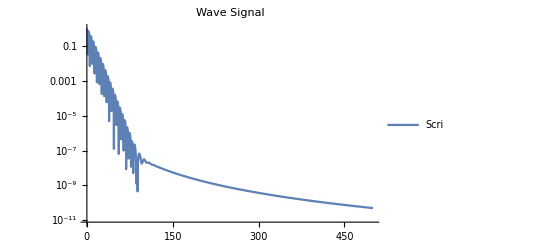

```mathematica
(*WaveBasis=hHrz;
SurfaceName="Horizon";*)

WaveBasis=hScri;
SurfaceName="Scri";

PlotStudy=ListLogPlot[
{Transpose@{Time,Abs@WaveBasis}
},
PlotLabel->"Wave Signal",
PlotLegends->{SurfaceName},
Joined->True
];
Show[PlotStudy]
```

Data Analysis (simple fit as easiest first option): 
(1) Blind test with unknown Amp and unknown ω
(2) Schwarzschild test with unknown Amp, but ω_Schwarz
(3) Elephant Flea test with unknown Amp, but ω_ElFlea

### Filter Fundamental QNM

```mathematica
Wave0= hQNM$Scri$ExactData[2] + hQNM$Scri$ExactData[3];


(*hQNM$Scri$ExactData[2]+hQNM$Scri$ExactData[3];*)
(*hQNM$Scri$ExactData[3];*)
(*hQNM$Scri$ExactData[2]+hQNM$Scri$ExactData[3];*)
(*Wave0=hQNM$Hrz$ExactData;*)

PlotExact=ListLogPlot[
{Transpose@{Time,Abs@WaveBasis},
Transpose@{Time,Abs@Wave0}
},
PlotLabels->{"Full Signal Num", "1stOrder-QNM (n=0) Exact"},
PlotLegends->SurfaceName,
Joined->True,
PlotRange->{{0,110},{10^-10,10}},
ImageSize->Scaled[0.8]
];
Show[PlotExact]
```

-Graphics-

```mathematica
WaveFilter0 = WaveBasis - Wave0;
Wave1=hQNM$Scri$ExactData[0]+hQNM$Scri$ExactData[1]+hQNM$Scri$ExactData[4]+hQNM$Scri$ExactData[5]+hQNM$Scri$ExactData[6]+hQNM$Scri$ExactData[7]+hQNM$Scri$ExactData[8];
(*hQNM$Scri$ExactData[2];*)
(*hQNM$Scri$ExactData[0]+hQNM$Scri$ExactData[1]+hQNM$Scri$ExactData[4]+hQNM$Scri$ExactData[5];*)
(*hQNM$Scri$ExactData[0]+hQNM$Scri$ExactData[1]+hQNM$Scri$ExactData[4]+hQNM$Scri$ExactData[5](*+hQNM$Scri$ExactData[6]*);*)
(*Wave1=hpp$HRz$ExactData*)

PlotFilter0=ListLogPlot[
{Transpose@{Time,Abs@WaveFilter0},
(*Transpose@{Time,Abs@hpm$HRz$ExactData}*)
Transpose@{Time,Abs@Wave1}
},
(*PlotLabels->{"Residual Signal (n=0)" , "2ndOrder-QNM (+-) Exact"},*)
PlotLabels->{"Residual Signal (n=0)" , "1stOrder-QNM (n=1) Exact"},
PlotLegends->SurfaceName,
Joined->True,
PlotRange->{{0,80},{10^-10,1}},
ImageSize->Scaled[0.8]
];
Show[PlotFilter0]
```

-Graphics-

### Filter First Overtone

```mathematica
WaveFilter1 =WaveFilter0-Wave1;
Wave2=hQNM$Scri$ExactData[0]+hQNM$Scri$ExactData[1]+hQNM$Scri$ExactData[4]+hQNM$Scri$ExactData[5];
(*Wave2=hpm$HRz$ExactData;*)

PlotFilter1=ListLogPlot[
{Transpose@{Time,Abs@WaveFilter1}(*,*)
(*Transpose@{Time,Abs@Wave2}*)
},
(*PlotLabels->{"Residual Signal (n=0, +-)" , "2ndOrder-QNM (++) Exact"},*)
PlotLabels->{"Residual Signal (n=0, n=1)" , "1stOrder-QNM (n=2) Exact"},
PlotLegends->SurfaceName,
Joined->True,
PlotRange->{{0,40},{10^-10,1}},
ImageSize->Scaled[0.8]
];
Show[PlotFilter1]
```

-Graphics-

### Filter Second Overtone

```mathematica
WaveFilter2 =WaveFilter1 - Wave2;
(*Wave3=hQNM$Scri$ExactData[3];*)
PlotFilter2=ListLogPlot[
{Transpose@{Time,Abs@WaveFilter2}(*,
Transpose@{Time,Abs@Wave3}*)
},
PlotLabels->{"Residual Signal (n=0, n=1, n=2)", "1stOrder-QNM (n=3) Exact"},
PlotLegends->SurfaceName,
Joined->True,
PlotRange->{{0,30},{10^-10,1}},
ImageSize->Scaled[0.8]
];
Show[PlotFilter2]
```

-Graphics-

```mathematica
hFIT=A*exp(s0*t)+B*exp(s1*t)
```

A exp s0 t+B exp s1 t

(i) We known s0 and s1 from freq. domain. Fit for A and B. Do we recover prediction from ID? Guess: Yes
(ii) Blind agnostic test: fit for (A,B, s0, s1). Do we recover the avoid crossing QNMs? Guess: No ?

## “Fourier” Analysis Time Domain Signal - Poor Man Data Analysis

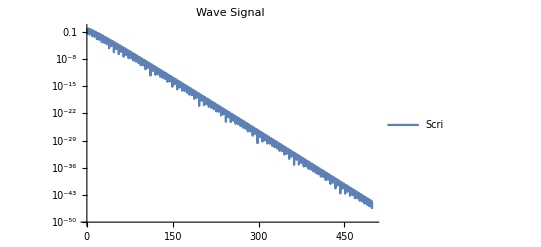

```mathematica
WaveStudy= hQNM$Scri$ExactData[1]+
hQNM$Scri$ExactData[2]+
hQNM$Scri$ExactData[3];
(*WaveBasis;*) (*Sum[hQNM$Scri$ExactData[i],{i,0,8}];*)

(*hQNM$Scri$ExactData[2]+hQNM$Scri$ExactData[3];*)

(*WaveBasis-(hQNM$Scri$ExactData[2]+hQNM$Scri$ExactData[3]);*)


(*hQNM$Scri$ExactData[2]+hQNM$Scri$ExactData[3];*)(*WaveBasis;*)
(*hQNM$Scri$ExactData[2]+hQNM$Scri$ExactData[3];*)
(*WaveBasis;*)

PlotTimeSignal=ListLogPlot[
{Transpose@{Time,Abs@WaveStudy}
},
PlotLabel->"Wave Signal",
PlotLegends->
{"Scri"},
Joined->True,
ImageSize->Scaled[0.8]
];
Show[PlotTimeSignal]
```

### Select QNM phase

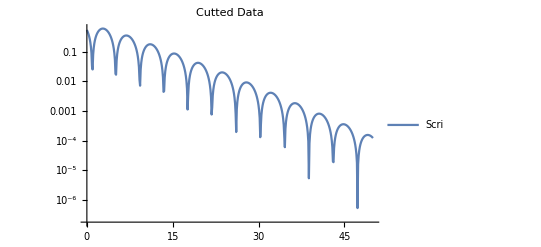

```mathematica
t0=0;I0=IndxT[t0];
t1=50; I1=IndxT[t1];
tData=Table[ Time[[i]],{i,I0,I1}];
Data=Table[WaveStudy[[i]],{i,I0,I1}];

NData=Length@Data;
PlotData=ListLogPlot[
{Transpose@{tData,Abs@Data}
},
PlotLabel->"Cutted Data",
PlotLegends->
{"Scri"},
Joined->True
];
Show[PlotData]
```

```mathematica
Data2Fit=Transpose@{tData,Data};

nQNM$Fit=2;

model=Sum [ A[i]*Exp[-ωi[i] *t]Sin[ϕ[i]+ωr[i]*t] ,{i,1,nQNM$Fit}]


modelpar=Table[{A[i],ϕ[i],ωi[i], ωr[i]},{i,1,nQNM$Fit}]//Flatten


nlm=NonlinearModelFit[Data2Fit,model,modelpar,t, MaxIterations->Infinity, AccuracyGoal->0.5*MachinePrecision, PrecisionGoal->0.5*MachinePrecision,  WorkingPrecision->MachinePrecision]//Normal
nlm$data=nlm/.t->tData;
Residual=Abs[Data-nlm$data]/Abs[Data];

FittedData=Transpose@{tData,nlm$data};
ResidualData=Transpose@{tData,Residual};

ListLogPlot[{Abs@Data2Fit,Abs@FittedData}, Joined->True, PlotLabels->{"Data", "Fit"}]
(*ListLogPlot[Abs@ResidualData, Joined->True, PlotLabels->{"Residual"}]*)
N@s$QNM
(*N@s$QNM[[3]]
N@s$QNM[[4]]

2*Abs[ηϕScri[[3]]]
2*Abs[ηϕScri[[4]]]

π+Arg[ηϕScri[[3]]]
π+Arg[ηϕScri[[4]]]*)
```

ⅇ^(-t ωi[1]) A[1] Sin[ϕ[1]+t ωr[1]]+ⅇ^(-t ωi[2]) A[2] Sin[ϕ[2]+t ωr[2]]

{A[1],ϕ[1],ωi[1],ωr[1],A[2],ϕ[2],ωi[2],ωr[2]}

FittedModel::precw: The precision of the argument function (MachinePrecision) is less than WorkingPrecision (MachinePrecision).

0.519128 ⅇ^(-0.346312 t) Sin[5.41346+0.62106 t]+1.27667 ⅇ^(-0.175684 t) Sin[2.32145+0.758236 t]

-Graphics-

{-0.304656-0.162407 ⅈ,-0.251156-0.433143 ⅈ,-0.217235-0.736313 ⅈ,-0.211645+0.739198 ⅈ,-0.36968+0.971584 ⅈ,-0.480186-1.18411 ⅈ,-0.588012+1.40296 ⅈ,-0.693698+1.62596 ⅈ,-0.797748+1.85165 ⅈ}

```mathematica
sSchwarzschil$n0=-0.1779246313778724125652120005152178509675423181561187703639623721770992017316962715759234642097336789737598225764160641944325887735662226216980430348181479+I* 0.747343368836081044564012120434754107823160172903535881938910623355711335675523008900239525461539174202261286644053489464729872338914566586615874614796782;
N[sSchwarzschil$n0,3]
```

-0.18+0.747 ⅈ

```mathematica
N@s$QNM
```

{-0.304656-0.162407 ⅈ,-0.251156-0.433143 ⅈ,-0.217235-0.736313 ⅈ,-0.211645+0.739198 ⅈ,-0.36968+0.971584 ⅈ,-0.480186-1.18411 ⅈ}

### Fourier Analysis

#### Poor-man Routine to read local maximum

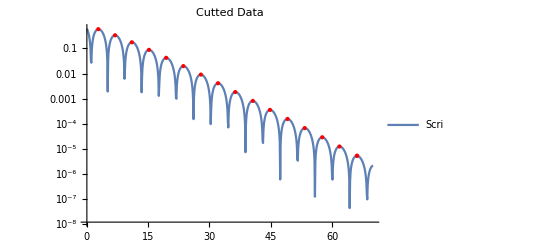

```mathematica
kmax=1;
kk=1;
MaxPos={};
While[kk<NData,
For[k=kmax+1, k<NData, k++,
Fm1=Abs@Data[[k-1]];
F=Abs@Data[[k]];
Fp1=Abs@Data[[k+1]];

If[F>Fm1 && F>Fp1,
kmaxt=k;
Break[];
];
];
kmax=kmaxt;
MaxPos=Append[MaxPos,kmax];
kk=k;
]
MaxSize=Length@MaxPos;
MaxData=Table[{tData[[MaxPos[[n]]]],Abs@Data[[MaxPos[[n]]  ]]}, {n,1,MaxSize}];
PlotMax=ListLogPlot[MaxData, PlotRange->Full, PlotStyle->{Red,PointSize[Medium]}];
Show[PlotData,PlotMax]
```

#### Fit Exponential

-0.18690669828540074

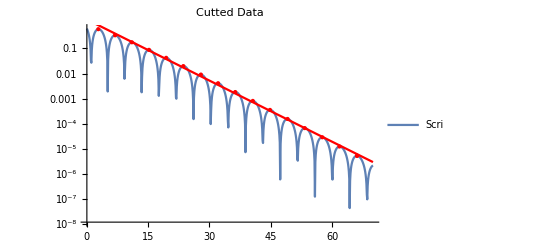

```mathematica
FitData=Table[{MaxData[[i,1]],Log@MaxData[[i,2]]},{i,1,MaxSize}];
FitExp=Fit[FitData,{1,t},t];
PlotFit=LogPlot[Exp@FitExp, {t,t0,t1}, PlotStyle->Red];
ωI=D[FitExp,t]
Show[PlotData,PlotMax, PlotFit]
```

#### Fourier Transform According to Help

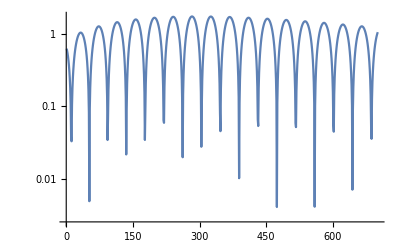

```mathematica
Period=Table[ Data[[k]]*Exp[-ωI*tData[[k]]], {k,1, NData}];
PlotPeriod=ListLogPlot[Abs@Period, PlotRange->Full, Joined->True];
Show[PlotPeriod]
```

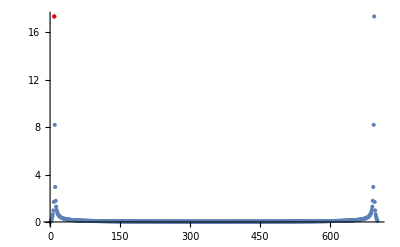

```mathematica
FourierPeriod=Abs[Fourier[Period]];

NFourier=Length@FourierPeriod;
FourierPeriod1=Table[FourierPeriod[[i]], {i,1,NFourier/2}];
FourierPeriod2=Table[FourierPeriod[[i-NFourier/2]], {i,NFourier/2+1,NFourier}];
pos = Position[FourierPeriod1, Max[FourierPeriod1]][[1,1]];


Show[ListPlot[FourierPeriod], Graphics[{Red, Point[{pos, FourierPeriod[[pos]]}]}], PlotRange->All]
```

```mathematica
fr = Abs[Fourier[Period Exp[2 Pi I (pos - 2) N[Range[0, NData - 1]]/NData], FourierParameters->{0,2/NData}]];
frpos = Position[fr, Max[fr]][[1,1]]
```

451

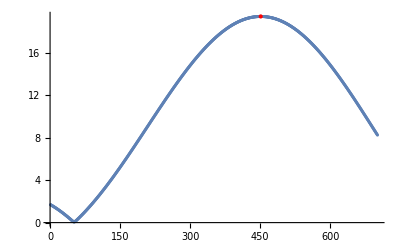

```mathematica
Show[ListPlot[fr], Graphics[{Red, Point[{frpos, fr[[frpos]]}]}], PlotRange->All]
```

```mathematica
Per=N[NData/(pos - 2 + 2 (frpos - 1)/NData)];
ωR=N[2*Pi/(Per*h)]
```

0.742499

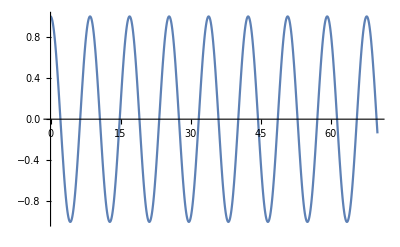

```mathematica
Plot[Cos[ωR*t], {t,t0,t1}]
```

#### Print Results

```mathematica
Print["Imaginary QNM ωI = ",ωI]
Print["Real QNM ωR  = ",ωR]
```

Imaginary QNM ωI = -0.18690669828540074

Real QNM ωR  = 0.742499

```mathematica
N[s$QNM]
```

{-0.304656-0.162407 ⅈ,-0.251156-0.433143 ⅈ,-0.217235-0.736313 ⅈ,-0.211645+0.739198 ⅈ,-0.36968+0.971584 ⅈ,-0.480186-1.18411 ⅈ}

```mathematica
s$mean=(N[s$QNM[[3]]]+Conjugate[N[s$QNM[[4]]]])/2
```

-0.21444-0.737755 ⅈ

```mathematica
sSchwarzschil$n0=-0.1779246313778724125652120005152178509675423181561187703639623721770992017316962715759234642097336789737598225764160641944325887735662226216980430348181479+I* 0.747343368836081044564012120434754107823160172903535881938910623355711335675523008900239525461539174202261286644053489464729872338914566586615874614796782;
N[sSchwarzschil$n0,3]
```

-0.18+0.747 ⅈ